# Random PoS reward function

## Variables

```mathematica
sequences = 5
n = 210
rewards = List[50*n,25*n,12.5*n,6.25*n,3.125*n]
r =0.03
```

5

210

{10500,5250,2625.,1312.5,656.25}

0.03

## Constant reward function

```mathematica
constreward[n_,R_,T_]=Table[R/T,n]
```

{R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T,R/T}

## Geometric reward function

```mathematica
geometricreward[n_, R_, T_] = Table[(1 + R)^(i/T) - (1 + R)^((i-1)/T),{i,n}]
```

{-1+(1+R)^(1/T),-(1+R)^(1/T)+(1+R)^(2/T),-(1+R)^(2/T)+(1+R)^(3/T),-(1+R)^(3/T)+(1+R)^(4/T),-(1+R)^(4/T)+(1+R)^(5/T),-(1+R)^(5/T)+(1+R)^(6/T),-(1+R)^(6/T)+(1+R)^(7/T),-(1+R)^(7/T)+(1+R)^(8/T),-(1+R)^(8/T)+(1+R)^(9/T),-(1+R)^(9/T)+(1+R)^(10/T),-(1+R)^(10/T)+(1+R)^(11/T),-(1+R)^(11/T)+(1+R)^(12/T),-(1+R)^(12/T)+(1+R)^(13/T),-(1+R)^(13/T)+(1+R)^(14/T),-(1+R)^(14/T)+(1+R)^(15/T),-(1+R)^(15/T)+(1+R)^(16/T),-(1+R)^(16/T)+(1+R)^(17/T),-(1+R)^(17/T)+(1+R)^(18/T),-(1+R)^(18/T)+(1+R)^(19/T),-(1+R)^(19/T)+(1+R)^(20/T),-(1+R)^(20/T)+(1+R)^(21/T),-(1+R)^(21/T)+(1+R)^(22/T),-(1+R)^(22/T)+(1+R)^(23/T),-(1+R)^(23/T)+(1+R)^(24/T),-(1+R)^(24/T)+(1+R)^(25/T),-(1+R)^(25/T)+(1+R)^(26/T),-(1+R)^(26/T)+(1+R)^(27/T),-(1+R)^(27/T)+(1+R)^(28/T),-(1+R)^(28/T)+(1+R)^(29/T),-(1+R)^(29/T)+(1+R)^(30/T),-(1+R)^(30/T)+(1+R)^(31/T),-(1+R)^(31/T)+(1+R)^(32/T),-(1+R)^(32/T)+(1+R)^(33/T),-(1+R)^(33/T)+(1+R)^(34/T),-(1+R)^(34/T)+(1+R)^(35/T),-(1+R)^(35/T)+(1+R)^(36/T),-(1+R)^(36/T)+(1+R)^(37/T),-(1+R)^(37/T)+(1+R)^(38/T),-(1+R)^(38/T)+(1+R)^(39/T),-(1+R)^(39/T)+(1+R)^(40/T),-(1+R)^(40/T)+(1+R)^(41/T),-(1+R)^(41/T)+(1+R)^(42/T),-(1+R)^(42/T)+(1+R)^(43/T),-(1+R)^(43/T)+(1+R)^(44/T),-(1+R)^(44/T)+(1+R)^(45/T),-(1+R)^(45/T)+(1+R)^(46/T),-(1+R)^(46/T)+(1+R)^(47/T),-(1+R)^(47/T)+(1+R)^(48/T),-(1+R)^(48/T)+(1+R)^(49/T),-(1+R)^(49/T)+(1+R)^(50/T),-(1+R)^(50/T)+(1+R)^(51/T),-(1+R)^(51/T)+(1+R)^(52/T),-(1+R)^(52/T)+(1+R)^(53/T),-(1+R)^(53/T)+(1+R)^(54/T),-(1+R)^(54/T)+(1+R)^(55/T),-(1+R)^(55/T)+(1+R)^(56/T),-(1+R)^(56/T)+(1+R)^(57/T),-(1+R)^(57/T)+(1+R)^(58/T),-(1+R)^(58/T)+(1+R)^(59/T),-(1+R)^(59/T)+(1+R)^(60/T),-(1+R)^(60/T)+(1+R)^(61/T),-(1+R)^(61/T)+(1+R)^(62/T),-(1+R)^(62/T)+(1+R)^(63/T),-(1+R)^(63/T)+(1+R)^(64/T),-(1+R)^(64/T)+(1+R)^(65/T),-(1+R)^(65/T)+(1+R)^(66/T),-(1+R)^(66/T)+(1+R)^(67/T),-(1+R)^(67/T)+(1+R)^(68/T),-(1+R)^(68/T)+(1+R)^(69/T),-(1+R)^(69/T)+(1+R)^(70/T),-(1+R)^(70/T)+(1+R)^(71/T),-(1+R)^(71/T)+(1+R)^(72/T),-(1+R)^(72/T)+(1+R)^(73/T),-(1+R)^(73/T)+(1+R)^(74/T),-(1+R)^(74/T)+(1+R)^(75/T),-(1+R)^(75/T)+(1+R)^(76/T),-(1+R)^(76/T)+(1+R)^(77/T),-(1+R)^(77/T)+(1+R)^(78/T),-(1+R)^(78/T)+(1+R)^(79/T),-(1+R)^(79/T)+(1+R)^(80/T),-(1+R)^(80/T)+(1+R)^(81/T),-(1+R)^(81/T)+(1+R)^(82/T),-(1+R)^(82/T)+(1+R)^(83/T),-(1+R)^(83/T)+(1+R)^(84/T),-(1+R)^(84/T)+(1+R)^(85/T),-(1+R)^(85/T)+(1+R)^(86/T),-(1+R)^(86/T)+(1+R)^(87/T),-(1+R)^(87/T)+(1+R)^(88/T),-(1+R)^(88/T)+(1+R)^(89/T),-(1+R)^(89/T)+(1+R)^(90/T),-(1+R)^(90/T)+(1+R)^(91/T),-(1+R)^(91/T)+(1+R)^(92/T),-(1+R)^(92/T)+(1+R)^(93/T),-(1+R)^(93/T)+(1+R)^(94/T),-(1+R)^(94/T)+(1+R)^(95/T),-(1+R)^(95/T)+(1+R)^(96/T),-(1+R)^(96/T)+(1+R)^(97/T),-(1+R)^(97/T)+(1+R)^(98/T),-(1+R)^(98/T)+(1+R)^(99/T),-(1+R)^(99/T)+(1+R)^(100/T),-(1+R)^(100/T)+(1+R)^(101/T),-(1+R)^(101/T)+(1+R)^(102/T),-(1+R)^(102/T)+(1+R)^(103/T),-(1+R)^(103/T)+(1+R)^(104/T),-(1+R)^(104/T)+(1+R)^(105/T),-(1+R)^(105/T)+(1+R)^(106/T),-(1+R)^(106/T)+(1+R)^(107/T),-(1+R)^(107/T)+(1+R)^(108/T),-(1+R)^(108/T)+(1+R)^(109/T),-(1+R)^(109/T)+(1+R)^(110/T),-(1+R)^(110/T)+(1+R)^(111/T),-(1+R)^(111/T)+(1+R)^(112/T),-(1+R)^(112/T)+(1+R)^(113/T),-(1+R)^(113/T)+(1+R)^(114/T),-(1+R)^(114/T)+(1+R)^(115/T),-(1+R)^(115/T)+(1+R)^(116/T),-(1+R)^(116/T)+(1+R)^(117/T),-(1+R)^(117/T)+(1+R)^(118/T),-(1+R)^(118/T)+(1+R)^(119/T),-(1+R)^(119/T)+(1+R)^(120/T),-(1+R)^(120/T)+(1+R)^(121/T),-(1+R)^(121/T)+(1+R)^(122/T),-(1+R)^(122/T)+(1+R)^(123/T),-(1+R)^(123/T)+(1+R)^(124/T),-(1+R)^(124/T)+(1+R)^(125/T),-(1+R)^(125/T)+(1+R)^(126/T),-(1+R)^(126/T)+(1+R)^(127/T),-(1+R)^(127/T)+(1+R)^(128/T),-(1+R)^(128/T)+(1+R)^(129/T),-(1+R)^(129/T)+(1+R)^(130/T),-(1+R)^(130/T)+(1+R)^(131/T),-(1+R)^(131/T)+(1+R)^(132/T),-(1+R)^(132/T)+(1+R)^(133/T),-(1+R)^(133/T)+(1+R)^(134/T),-(1+R)^(134/T)+(1+R)^(135/T),-(1+R)^(135/T)+(1+R)^(136/T),-(1+R)^(136/T)+(1+R)^(137/T),-(1+R)^(137/T)+(1+R)^(138/T),-(1+R)^(138/T)+(1+R)^(139/T),-(1+R)^(139/T)+(1+R)^(140/T),-(1+R)^(140/T)+(1+R)^(141/T),-(1+R)^(141/T)+(1+R)^(142/T),-(1+R)^(142/T)+(1+R)^(143/T),-(1+R)^(143/T)+(1+R)^(144/T),-(1+R)^(144/T)+(1+R)^(145/T),-(1+R)^(145/T)+(1+R)^(146/T),-(1+R)^(146/T)+(1+R)^(147/T),-(1+R)^(147/T)+(1+R)^(148/T),-(1+R)^(148/T)+(1+R)^(149/T),-(1+R)^(149/T)+(1+R)^(150/T),-(1+R)^(150/T)+(1+R)^(151/T),-(1+R)^(151/T)+(1+R)^(152/T),-(1+R)^(152/T)+(1+R)^(153/T),-(1+R)^(153/T)+(1+R)^(154/T),-(1+R)^(154/T)+(1+R)^(155/T),-(1+R)^(155/T)+(1+R)^(156/T),-(1+R)^(156/T)+(1+R)^(157/T),-(1+R)^(157/T)+(1+R)^(158/T),-(1+R)^(158/T)+(1+R)^(159/T),-(1+R)^(159/T)+(1+R)^(160/T),-(1+R)^(160/T)+(1+R)^(161/T),-(1+R)^(161/T)+(1+R)^(162/T),-(1+R)^(162/T)+(1+R)^(163/T),-(1+R)^(163/T)+(1+R)^(164/T),-(1+R)^(164/T)+(1+R)^(165/T),-(1+R)^(165/T)+(1+R)^(166/T),-(1+R)^(166/T)+(1+R)^(167/T),-(1+R)^(167/T)+(1+R)^(168/T),-(1+R)^(168/T)+(1+R)^(169/T),-(1+R)^(169/T)+(1+R)^(170/T),-(1+R)^(170/T)+(1+R)^(171/T),-(1+R)^(171/T)+(1+R)^(172/T),-(1+R)^(172/T)+(1+R)^(173/T),-(1+R)^(173/T)+(1+R)^(174/T),-(1+R)^(174/T)+(1+R)^(175/T),-(1+R)^(175/T)+(1+R)^(176/T),-(1+R)^(176/T)+(1+R)^(177/T),-(1+R)^(177/T)+(1+R)^(178/T),-(1+R)^(178/T)+(1+R)^(179/T),-(1+R)^(179/T)+(1+R)^(180/T),-(1+R)^(180/T)+(1+R)^(181/T),-(1+R)^(181/T)+(1+R)^(182/T),-(1+R)^(182/T)+(1+R)^(183/T),-(1+R)^(183/T)+(1+R)^(184/T),-(1+R)^(184/T)+(1+R)^(185/T),-(1+R)^(185/T)+(1+R)^(186/T),-(1+R)^(186/T)+(1+R)^(187/T),-(1+R)^(187/T)+(1+R)^(188/T),-(1+R)^(188/T)+(1+R)^(189/T),-(1+R)^(189/T)+(1+R)^(190/T),-(1+R)^(190/T)+(1+R)^(191/T),-(1+R)^(191/T)+(1+R)^(192/T),-(1+R)^(192/T)+(1+R)^(193/T),-(1+R)^(193/T)+(1+R)^(194/T),-(1+R)^(194/T)+(1+R)^(195/T),-(1+R)^(195/T)+(1+R)^(196/T),-(1+R)^(196/T)+(1+R)^(197/T),-(1+R)^(197/T)+(1+R)^(198/T),-(1+R)^(198/T)+(1+R)^(199/T),-(1+R)^(199/T)+(1+R)^(200/T),-(1+R)^(200/T)+(1+R)^(201/T),-(1+R)^(201/T)+(1+R)^(202/T),-(1+R)^(202/T)+(1+R)^(203/T),-(1+R)^(203/T)+(1+R)^(204/T),-(1+R)^(204/T)+(1+R)^(205/T),-(1+R)^(205/T)+(1+R)^(206/T),-(1+R)^(206/T)+(1+R)^(207/T),-(1+R)^(207/T)+(1+R)^(208/T),-(1+R)^(208/T)+(1+R)^(209/T),-(1+R)^(209/T)+(1+R)^(210/T)}

## Random reward function

```mathematica
randomreward[n_, R_, T_] = RandomVariate[UniformDistribution[{0.5,1.5}],n]*R/T
```

{(0.854819 R)/T,(0.575443 R)/T,(1.2036 R)/T,(0.718091 R)/T,(0.809297 R)/T,(1.01184 R)/T,(0.562356 R)/T,(1.30738 R)/T,(1.30667 R)/T,(0.993652 R)/T,(0.60348 R)/T,(0.530565 R)/T,(1.0817 R)/T,(1.08879 R)/T,(1.46657 R)/T,(1.45079 R)/T,(0.747339 R)/T,(0.648604 R)/T,(1.47217 R)/T,(0.694725 R)/T,(0.876143 R)/T,(1.11199 R)/T,(0.953417 R)/T,(0.900984 R)/T,(0.82047 R)/T,(0.663086 R)/T,(1.26809 R)/T,(0.565786 R)/T,(1.24946 R)/T,(1.00541 R)/T,(0.702787 R)/T,(1.34512 R)/T,(0.676392 R)/T,(1.17834 R)/T,(1.24692 R)/T,(1.42485 R)/T,(1.25756 R)/T,(1.25307 R)/T,(1.37088 R)/T,(1.41751 R)/T,(1.3034 R)/T,(0.504898 R)/T,(1.20189 R)/T,(0.904729 R)/T,(1.28238 R)/T,(1.06039 R)/T,(0.575784 R)/T,(0.506974 R)/T,(0.612963 R)/T,(1.08208 R)/T,(0.792753 R)/T,(0.612565 R)/T,(0.755319 R)/T,(0.835501 R)/T,(1.44061 R)/T,(0.676164 R)/T,(1.32573 R)/T,(1.49086 R)/T,(1.20011 R)/T,(1.03318 R)/T,(1.44789 R)/T,(1.21333 R)/T,(0.745704 R)/T,(1.03409 R)/T,(0.601636 R)/T,(1.03441 R)/T,(1.03873 R)/T,(1.24327 R)/T,(0.859854 R)/T,(1.23193 R)/T,(1.01697 R)/T,(1.24418 R)/T,(0.889714 R)/T,(1.25617 R)/T,(0.772089 R)/T,(1.29232 R)/T,(0.897506 R)/T,(1.09385 R)/T,(0.887576 R)/T,(1.26164 R)/T,(0.63676 R)/T,(1.4579 R)/T,(1.01064 R)/T,(0.875879 R)/T,(1.07064 R)/T,(0.753958 R)/T,(0.6652 R)/T,(0.631001 R)/T,(1.27731 R)/T,(1.29506 R)/T,(1.17786 R)/T,(0.716704 R)/T,(1.06324 R)/T,(1.09206 R)/T,(1.25987 R)/T,(0.530053 R)/T,(1.49805 R)/T,(1.36034 R)/T,(0.527151 R)/T,(1.14058 R)/T,(0.728341 R)/T,(1.00514 R)/T,(1.26629 R)/T,(0.887645 R)/T,(1.37446 R)/T,(1.03949 R)/T,(1.14594 R)/T,(1.30985 R)/T,(1.31628 R)/T,(0.982455 R)/T,(0.621393 R)/T,(0.661988 R)/T,(0.617557 R)/T,(1.00297 R)/T,(0.793232 R)/T,(0.855309 R)/T,(1.32824 R)/T,(1.17027 R)/T,(1.09629 R)/T,(1.42155 R)/T,(0.923242 R)/T,(0.828909 R)/T,(0.6365 R)/T,(1.12877 R)/T,(0.863352 R)/T,(1.43796 R)/T,(1.02618 R)/T,(0.943351 R)/T,(1.02364 R)/T,(0.664519 R)/T,(0.802044 R)/T,(1.09617 R)/T,(1.48242 R)/T,(1.32201 R)/T,(1.09607 R)/T,(1.28501 R)/T,(0.66431 R)/T,(0.811673 R)/T,(0.616273 R)/T,(0.890464 R)/T,(0.872657 R)/T,(0.999251 R)/T,(0.633418 R)/T,(1.45189 R)/T,(1.26525 R)/T,(0.545205 R)/T,(1.09467 R)/T,(0.511244 R)/T,(1.44844 R)/T,(0.887072 R)/T,(0.766363 R)/T,(1.35734 R)/T,(1.23572 R)/T,(1.24233 R)/T,(1.14867 R)/T,(0.521663 R)/T,(1.2292 R)/T,(0.842201 R)/T,(0.765075 R)/T,(1.13538 R)/T,(0.583564 R)/T,(1.15202 R)/T,(0.783732 R)/T,(1.04157 R)/T,(1.18219 R)/T,(0.620419 R)/T,(0.621899 R)/T,(1.09697 R)/T,(0.526346 R)/T,(0.873809 R)/T,(1.36172 R)/T,(0.504947 R)/T,(0.8659 R)/T,(1.21568 R)/T,(1.01928 R)/T,(1.22197 R)/T,(1.45438 R)/T,(0.976175 R)/T,(1.39046 R)/T,(1.34706 R)/T,(1.09395 R)/T,(0.668846 R)/T,(1.45705 R)/T,(1.41169 R)/T,(1.31547 R)/T,(1.2732 R)/T,(0.563992 R)/T,(0.937724 R)/T,(0.704334 R)/T,(1.27346 R)/T,(0.668229 R)/T,(0.613919 R)/T,(1.01901 R)/T,(0.757607 R)/T,(0.628746 R)/T,(0.660729 R)/T,(1.21195 R)/T,(0.81278 R)/T,(1.43566 R)/T,(1.242 R)/T,(1.35943 R)/T,(0.738493 R)/T,(1.41984 R)/T,(1.32604 R)/T,(1.02247 R)/T,(0.990263 R)/T,(0.946591 R)/T,(1.49609 R)/T,(0.761591 R)/T,(0.680862 R)/T}

```mathematica
randomdistribution[n_, R_, T_] = (RandomVariate[BetaDistribution[2,5],n]+0.5)*R/T
```

{(0.543603 R)/T,(0.852755 R)/T,(0.756339 R)/T,(0.644121 R)/T,(0.763489 R)/T,(0.796594 R)/T,(0.82236 R)/T,(0.859688 R)/T,(0.645908 R)/T,(0.588737 R)/T,(0.678228 R)/T,(0.69939 R)/T,(0.724772 R)/T,(0.634968 R)/T,(0.738088 R)/T,(0.575911 R)/T,(0.59841 R)/T,(0.668981 R)/T,(0.719197 R)/T,(0.810889 R)/T,(0.954993 R)/T,(0.526325 R)/T,(0.674673 R)/T,(0.860212 R)/T,(0.713135 R)/T,(0.856648 R)/T,(0.617299 R)/T,(0.753438 R)/T,(0.973015 R)/T,(1.05528 R)/T,(0.599218 R)/T,(0.887682 R)/T,(0.81988 R)/T,(0.67193 R)/T,(0.632926 R)/T,(1.20128 R)/T,(0.706662 R)/T,(0.717517 R)/T,(0.987295 R)/T,(0.746184 R)/T,(0.91075 R)/T,(0.765979 R)/T,(0.867918 R)/T,(0.690392 R)/T,(0.803679 R)/T,(0.761643 R)/T,(0.625001 R)/T,(0.687782 R)/T,(0.823794 R)/T,(0.666769 R)/T,(0.742361 R)/T,(0.901604 R)/T,(1.19621 R)/T,(0.898733 R)/T,(0.613461 R)/T,(1.07808 R)/T,(0.689755 R)/T,(0.760116 R)/T,(0.750448 R)/T,(0.739592 R)/T,(0.839879 R)/T,(0.611295 R)/T,(0.909986 R)/T,(0.747123 R)/T,(0.569862 R)/T,(0.869125 R)/T,(0.883542 R)/T,(0.809923 R)/T,(1.0396 R)/T,(0.881092 R)/T,(1.04477 R)/T,(0.814933 R)/T,(0.675771 R)/T,(0.677758 R)/T,(0.78084 R)/T,(0.599233 R)/T,(0.976968 R)/T,(0.59726 R)/T,(1.05956 R)/T,(1.01967 R)/T,(0.916657 R)/T,(0.554654 R)/T,(0.702824 R)/T,(0.565462 R)/T,(0.580594 R)/T,(0.962952 R)/T,(0.843142 R)/T,(0.636016 R)/T,(0.957867 R)/T,(1.12761 R)/T,(0.533098 R)/T,(0.897989 R)/T,(0.772327 R)/T,(0.978227 R)/T,(0.821304 R)/T,(0.622592 R)/T,(0.719674 R)/T,(0.505564 R)/T,(0.617035 R)/T,(0.765113 R)/T,(0.883135 R)/T,(0.841454 R)/T,(0.823912 R)/T,(0.616292 R)/T,(0.693402 R)/T,(0.667959 R)/T,(0.615695 R)/T,(0.74857 R)/T,(1.14154 R)/T,(0.961937 R)/T,(0.837914 R)/T,(0.77365 R)/T,(0.797557 R)/T,(1.04423 R)/T,(1.03462 R)/T,(0.619246 R)/T,(0.696951 R)/T,(0.874684 R)/T,(1.1088 R)/T,(0.552498 R)/T,(0.636582 R)/T,(0.599249 R)/T,(0.599926 R)/T,(1.13635 R)/T,(0.778388 R)/T,(0.789248 R)/T,(0.959521 R)/T,(0.664634 R)/T,(0.637219 R)/T,(0.636816 R)/T,(0.629968 R)/T,(1.22805 R)/T,(0.560841 R)/T,(0.617902 R)/T,(0.82861 R)/T,(0.584126 R)/T,(0.873548 R)/T,(0.551183 R)/T,(0.778387 R)/T,(0.725894 R)/T,(0.827683 R)/T,(0.73286 R)/T,(0.677109 R)/T,(0.798644 R)/T,(0.903793 R)/T,(1.02477 R)/T,(0.720097 R)/T,(0.784384 R)/T,(1.14321 R)/T,(0.915969 R)/T,(0.650499 R)/T,(0.947036 R)/T,(0.718018 R)/T,(0.723019 R)/T,(0.655833 R)/T,(0.7196 R)/T,(0.657257 R)/T,(1.06483 R)/T,(1.18017 R)/T,(0.825228 R)/T,(0.649139 R)/T,(0.995294 R)/T,(0.622984 R)/T,(0.894197 R)/T,(0.631841 R)/T,(0.548815 R)/T,(0.822451 R)/T,(0.609704 R)/T,(0.691764 R)/T,(0.884757 R)/T,(0.645918 R)/T,(0.93434 R)/T,(0.882684 R)/T,(0.645204 R)/T,(0.844531 R)/T,(0.73416 R)/T,(0.686214 R)/T,(0.566521 R)/T,(0.865239 R)/T,(0.696418 R)/T,(0.809163 R)/T,(1.13076 R)/T,(0.966562 R)/T,(0.577355 R)/T,(0.658673 R)/T,(0.992377 R)/T,(0.733939 R)/T,(0.860903 R)/T,(0.678601 R)/T,(0.575233 R)/T,(0.905825 R)/T,(0.568813 R)/T,(0.894997 R)/T,(0.760855 R)/T,(0.710793 R)/T,(0.777047 R)/T,(0.812719 R)/T,(0.796813 R)/T,(0.561376 R)/T,(0.613967 R)/T,(0.893732 R)/T,(1.03894 R)/T,(0.693461 R)/T,(0.55011 R)/T,(0.875433 R)/T,(0.830118 R)/T,(0.605302 R)/T,(0.73689 R)/T,(0.626202 R)/T,(0.582966 R)/T}

## Interest rate function

```mathematica
interestreward[n_, r_, T_] = (1+r/n)^(n*T)
```

1.00014^(210 T)

## Comparison

```mathematica
dataconst= Flatten[Table[constreward[runs, rewards[[i]], n],{i,1,sequences}]]
datageometric = Flatten[Table[geometricreward[runs, rewards[[i]], n],{i,1,sequences}]]
datarandom = Flatten[Table[randomreward[runs, rewards[[i]], n],{i,1,sequences}]]
datarandomdist = Flatten[Table[randomdistribution[runs, rewards[[i]], n],{i,1,sequences}]]
plotdata= List[dataconst,datageometric, datarandom, datarandomdist]
```

{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125}

{-1+10501^(1/210),-10501^(1/210)+10501^(1/105),-10501^(1/105)+10501^(1/70),-10501^(1/70)+10501^(2/105),-10501^(2/105)+10501^(1/42),-10501^(1/42)+10501^(1/35),-10501^(1/35)+10501^(1/30),-10501^(1/30)+10501^(4/105),-10501^(4/105)+10501^(3/70),-10501^(3/70)+10501^(1/21),-10501^(1/21)+10501^(11/210),-10501^(11/210)+10501^(2/35),-10501^(2/35)+10501^(13/210),-10501^(13/210)+10501^(1/15),-10501^(1/15)+10501^(1/14),-10501^(1/14)+10501^(8/105),-10501^(8/105)+10501^(17/210),-10501^(17/210)+10501^(3/35),-10501^(3/35)+10501^(19/210),-10501^(19/210)+10501^(2/21),-10501^(2/21)+10501^(1/10),-10501^(1/10)+10501^(11/105),-10501^(11/105)+10501^(23/210),-10501^(23/210)+10501^(4/35),-10501^(4/35)+10501^(5/42),-10501^(5/42)+10501^(13/105),-10501^(13/105)+10501^(9/70),-10501^(9/70)+10501^(2/15),-10501^(2/15)+10501^(29/210),-10501^(29/210)+10501^(1/7),-10501^(1/7)+10501^(31/210),-10501^(31/210)+10501^(16/105),-10501^(16/105)+10501^(11/70),-10501^(11/70)+10501^(17/105),-10501^(17/105)+10501^(1/6),-10501^(1/6)+10501^(6/35),-10501^(6/35)+10501^(37/210),-10501^(37/210)+10501^(19/105),-10501^(19/105)+10501^(13/70),-10501^(13/70)+10501^(4/21),-10501^(4/21)+10501^(41/210),-10501^(41/210)+10501^(1/5),-10501^(1/5)+10501^(43/210),-10501^(43/210)+10501^(22/105),-10501^(22/105)+10501^(3/14),-10501^(3/14)+10501^(23/105),-10501^(23/105)+10501^(47/210),-10501^(47/210)+10501^(8/35),-10501^(8/35)+10501^(7/30),-10501^(7/30)+10501^(5/21),-10501^(5/21)+10501^(17/70),-10501^(17/70)+10501^(26/105),-10501^(26/105)+10501^(53/210),-10501^(53/210)+10501^(9/35),-10501^(9/35)+10501^(11/42),-10501^(11/42)+10501^(4/15),-10501^(4/15)+10501^(19/70),-10501^(19/70)+10501^(29/105),-10501^(29/105)+10501^(59/210),-10501^(59/210)+10501^(2/7),-10501^(2/7)+10501^(61/210),-10501^(61/210)+10501^(31/105),-10501^(31/105)+10501^(3/10),-10501^(3/10)+10501^(32/105),-10501^(32/105)+10501^(13/42),-10501^(13/42)+10501^(11/35),-10501^(11/35)+10501^(67/210),-10501^(67/210)+10501^(34/105),-10501^(34/105)+10501^(23/70),-10501^(23/70)+10501^(1/3),-10501^(1/3)+10501^(71/210),-10501^(71/210)+10501^(12/35),-10501^(12/35)+10501^(73/210),-10501^(73/210)+10501^(37/105),-10501^(37/105)+10501^(5/14),-10501^(5/14)+10501^(38/105),-10501^(38/105)+10501^(11/30),-10501^(11/30)+10501^(13/35),-10501^(13/35)+10501^(79/210),-10501^(79/210)+10501^(8/21),-10501^(8/21)+10501^(27/70),-10501^(27/70)+10501^(41/105),-10501^(41/105)+10501^(83/210),-10501^(83/210)+10501^(2/5),-10501^(2/5)+10501^(17/42),-10501^(17/42)+10501^(43/105),-10501^(43/105)+10501^(29/70),-10501^(29/70)+10501^(44/105),-10501^(44/105)+10501^(89/210),-10501^(89/210)+10501^(3/7),-10501^(3/7)+10501^(13/30),-10501^(13/30)+10501^(46/105),-10501^(46/105)+10501^(31/70),-10501^(31/70)+10501^(47/105),-10501^(47/105)+10501^(19/42),-10501^(19/42)+10501^(16/35),-10501^(16/35)+10501^(97/210),-10501^(97/210)+10501^(7/15),-10501^(7/15)+10501^(33/70),-10501^(33/70)+10501^(10/21),-10501^(10/21)+10501^(101/210),-10501^(101/210)+10501^(17/35),-10501^(17/35)+10501^(103/210),-10501^(103/210)+10501^(52/105),-10501^(52/105)+√10501,-√10501+10501^(53/105),-10501^(53/105)+10501^(107/210),-10501^(107/210)+10501^(18/35),-10501^(18/35)+10501^(109/210),-10501^(109/210)+10501^(11/21),-10501^(11/21)+10501^(37/70),-10501^(37/70)+10501^(8/15),-10501^(8/15)+10501^(113/210),-10501^(113/210)+10501^(19/35),-10501^(19/35)+10501^(23/42),-10501^(23/42)+10501^(58/105),-10501^(58/105)+10501^(39/70),-10501^(39/70)+10501^(59/105),-10501^(59/105)+10501^(17/30),-10501^(17/30)+10501^(4/7),-10501^(4/7)+10501^(121/210),-10501^(121/210)+10501^(61/105),-10501^(61/105)+10501^(41/70),-10501^(41/70)+10501^(62/105),-10501^(62/105)+10501^(25/42),-10501^(25/42)+10501^(3/5),-10501^(3/5)+10501^(127/210),-10501^(127/210)+10501^(64/105),-10501^(64/105)+10501^(43/70),-10501^(43/70)+10501^(13/21),-10501^(13/21)+10501^(131/210),-10501^(131/210)+10501^(22/35),-10501^(22/35)+10501^(19/30),-10501^(19/30)+10501^(67/105),-10501^(67/105)+10501^(9/14),-10501^(9/14)+10501^(68/105),-10501^(68/105)+10501^(137/210),-10501^(137/210)+10501^(23/35),-10501^(23/35)+10501^(139/210),-10501^(139/210)+10501^(2/3),-10501^(2/3)+10501^(47/70),-10501^(47/70)+10501^(71/105),-10501^(71/105)+10501^(143/210),-10501^(143/210)+10501^(24/35),-10501^(24/35)+10501^(29/42),-10501^(29/42)+10501^(73/105),-10501^(73/105)+10501^(7/10),-10501^(7/10)+10501^(74/105),-10501^(74/105)+10501^(149/210),-10501^(149/210)+10501^(5/7),-10501^(5/7)+10501^(151/210),-10501^(151/210)+10501^(76/105),-10501^(76/105)+10501^(51/70),-10501^(51/70)+10501^(11/15),-10501^(11/15)+10501^(31/42),-10501^(31/42)+10501^(26/35),-10501^(26/35)+10501^(157/210),-10501^(157/210)+10501^(79/105),-10501^(79/105)+10501^(53/70),-10501^(53/70)+10501^(16/21),-10501^(16/21)+10501^(23/30),-10501^(23/30)+10501^(27/35),-10501^(27/35)+10501^(163/210),-10501^(163/210)+10501^(82/105),-10501^(82/105)+10501^(11/14),-10501^(11/14)+10501^(83/105),-10501^(83/105)+10501^(167/210),-10501^(167/210)+10501^(4/5),-10501^(4/5)+10501^(169/210),-10501^(169/210)+10501^(17/21),-10501^(17/21)+10501^(57/70),-10501^(57/70)+10501^(86/105),-10501^(86/105)+10501^(173/210),-10501^(173/210)+10501^(29/35),-10501^(29/35)+10501^(5/6),-10501^(5/6)+10501^(88/105),-10501^(88/105)+10501^(59/70),-10501^(59/70)+10501^(89/105),-10501^(89/105)+10501^(179/210),-10501^(179/210)+10501^(6/7),-10501^(6/7)+10501^(181/210),-10501^(181/210)+10501^(13/15),-10501^(13/15)+10501^(61/70),-10501^(61/70)+10501^(92/105),-10501^(92/105)+10501^(37/42),-10501^(37/42)+10501^(31/35),-10501^(31/35)+10501^(187/210),-10501^(187/210)+10501^(94/105),-10501^(94/105)+10501^(9/10),-10501^(9/10)+10501^(19/21),-10501^(19/21)+10501^(191/210),-10501^(191/210)+10501^(32/35),-10501^(32/35)+10501^(193/210),-10501^(193/210)+10501^(97/105),-10501^(97/105)+10501^(13/14),-10501^(13/14)+10501^(14/15),-10501^(14/15)+10501^(197/210),-10501^(197/210)+10501^(33/35),-10501^(33/35)+10501^(199/210),-10501^(199/210)+10501^(20/21),-10501^(20/21)+10501^(67/70),-10501^(67/70)+10501^(101/105),-10501^(101/105)+10501^(29/30),-10501^(29/30)+10501^(34/35),-10501^(34/35)+10501^(41/42),-10501^(41/42)+10501^(103/105),-10501^(103/105)+10501^(69/70),-10501^(69/70)+10501^(104/105),-10501^(104/105)+10501^(209/210),10501-10501^(209/210),-1+5251^(1/210),-5251^(1/210)+5251^(1/105),-5251^(1/105)+5251^(1/70),-5251^(1/70)+5251^(2/105),-5251^(2/105)+5251^(1/42),-5251^(1/42)+5251^(1/35),-5251^(1/35)+5251^(1/30),-5251^(1/30)+5251^(4/105),-5251^(4/105)+5251^(3/70),-5251^(3/70)+5251^(1/21),-5251^(1/21)+5251^(11/210),-5251^(11/210)+5251^(2/35),-5251^(2/35)+5251^(13/210),-5251^(13/210)+5251^(1/15),-5251^(1/15)+5251^(1/14),-5251^(1/14)+5251^(8/105),-5251^(8/105)+5251^(17/210),-5251^(17/210)+5251^(3/35),-5251^(3/35)+5251^(19/210),-5251^(19/210)+5251^(2/21),-5251^(2/21)+5251^(1/10),-5251^(1/10)+5251^(11/105),-5251^(11/105)+5251^(23/210),-5251^(23/210)+5251^(4/35),-5251^(4/35)+5251^(5/42),-5251^(5/42)+5251^(13/105),-5251^(13/105)+5251^(9/70),-5251^(9/70)+5251^(2/15),-5251^(2/15)+5251^(29/210),-5251^(29/210)+5251^(1/7),-5251^(1/7)+5251^(31/210),-5251^(31/210)+5251^(16/105),-5251^(16/105)+5251^(11/70),-5251^(11/70)+5251^(17/105),-5251^(17/105)+5251^(1/6),-5251^(1/6)+5251^(6/35),-5251^(6/35)+5251^(37/210),-5251^(37/210)+5251^(19/105),-5251^(19/105)+5251^(13/70),-5251^(13/70)+5251^(4/21),-5251^(4/21)+5251^(41/210),-5251^(41/210)+5251^(1/5),-5251^(1/5)+5251^(43/210),-5251^(43/210)+5251^(22/105),-5251^(22/105)+5251^(3/14),-5251^(3/14)+5251^(23/105),-5251^(23/105)+5251^(47/210),-5251^(47/210)+5251^(8/35),-5251^(8/35)+5251^(7/30),-5251^(7/30)+5251^(5/21),-5251^(5/21)+5251^(17/70),-5251^(17/70)+5251^(26/105),-5251^(26/105)+5251^(53/210),-5251^(53/210)+5251^(9/35),-5251^(9/35)+5251^(11/42),-5251^(11/42)+5251^(4/15),-5251^(4/15)+5251^(19/70),-5251^(19/70)+5251^(29/105),-5251^(29/105)+5251^(59/210),-5251^(59/210)+5251^(2/7),-5251^(2/7)+5251^(61/210),-5251^(61/210)+5251^(31/105),-5251^(31/105)+5251^(3/10),-5251^(3/10)+5251^(32/105),-5251^(32/105)+5251^(13/42),-5251^(13/42)+5251^(11/35),-5251^(11/35)+5251^(67/210),-5251^(67/210)+5251^(34/105),-5251^(34/105)+5251^(23/70),-5251^(23/70)+5251^(1/3),-5251^(1/3)+5251^(71/210),-5251^(71/210)+5251^(12/35),-5251^(12/35)+5251^(73/210),-5251^(73/210)+5251^(37/105),-5251^(37/105)+5251^(5/14),-5251^(5/14)+5251^(38/105),-5251^(38/105)+5251^(11/30),-5251^(11/30)+5251^(13/35),-5251^(13/35)+5251^(79/210),-5251^(79/210)+5251^(8/21),-5251^(8/21)+5251^(27/70),-5251^(27/70)+5251^(41/105),-5251^(41/105)+5251^(83/210),-5251^(83/210)+5251^(2/5),-5251^(2/5)+5251^(17/42),-5251^(17/42)+5251^(43/105),-5251^(43/105)+5251^(29/70),-5251^(29/70)+5251^(44/105),-5251^(44/105)+5251^(89/210),-5251^(89/210)+5251^(3/7),-5251^(3/7)+5251^(13/30),-5251^(13/30)+5251^(46/105),-5251^(46/105)+5251^(31/70),-5251^(31/70)+5251^(47/105),-5251^(47/105)+5251^(19/42),-5251^(19/42)+5251^(16/35),-5251^(16/35)+5251^(97/210),-5251^(97/210)+5251^(7/15),-5251^(7/15)+5251^(33/70),-5251^(33/70)+5251^(10/21),-5251^(10/21)+5251^(101/210),-5251^(101/210)+5251^(17/35),-5251^(17/35)+5251^(103/210),-5251^(103/210)+5251^(52/105),-5251^(52/105)+√5251,-√5251+5251^(53/105),-5251^(53/105)+5251^(107/210),-5251^(107/210)+5251^(18/35),-5251^(18/35)+5251^(109/210),-5251^(109/210)+5251^(11/21),-5251^(11/21)+5251^(37/70),-5251^(37/70)+5251^(8/15),-5251^(8/15)+5251^(113/210),-5251^(113/210)+5251^(19/35),-5251^(19/35)+5251^(23/42),-5251^(23/42)+5251^(58/105),-5251^(58/105)+5251^(39/70),-5251^(39/70)+5251^(59/105),-5251^(59/105)+5251^(17/30),-5251^(17/30)+5251^(4/7),-5251^(4/7)+5251^(121/210),-5251^(121/210)+5251^(61/105),-5251^(61/105)+5251^(41/70),-5251^(41/70)+5251^(62/105),-5251^(62/105)+5251^(25/42),-5251^(25/42)+5251^(3/5),-5251^(3/5)+5251^(127/210),-5251^(127/210)+5251^(64/105),-5251^(64/105)+5251^(43/70),-5251^(43/70)+5251^(13/21),-5251^(13/21)+5251^(131/210),-5251^(131/210)+5251^(22/35),-5251^(22/35)+5251^(19/30),-5251^(19/30)+5251^(67/105),-5251^(67/105)+5251^(9/14),-5251^(9/14)+5251^(68/105),-5251^(68/105)+5251^(137/210),-5251^(137/210)+5251^(23/35),-5251^(23/35)+5251^(139/210),-5251^(139/210)+5251^(2/3),-5251^(2/3)+5251^(47/70),-5251^(47/70)+5251^(71/105),-5251^(71/105)+5251^(143/210),-5251^(143/210)+5251^(24/35),-5251^(24/35)+5251^(29/42),-5251^(29/42)+5251^(73/105),-5251^(73/105)+5251^(7/10),-5251^(7/10)+5251^(74/105),-5251^(74/105)+5251^(149/210),-5251^(149/210)+5251^(5/7),-5251^(5/7)+5251^(151/210),-5251^(151/210)+5251^(76/105),-5251^(76/105)+5251^(51/70),-5251^(51/70)+5251^(11/15),-5251^(11/15)+5251^(31/42),-5251^(31/42)+5251^(26/35),-5251^(26/35)+5251^(157/210),-5251^(157/210)+5251^(79/105),-5251^(79/105)+5251^(53/70),-5251^(53/70)+5251^(16/21),-5251^(16/21)+5251^(23/30),-5251^(23/30)+5251^(27/35),-5251^(27/35)+5251^(163/210),-5251^(163/210)+5251^(82/105),-5251^(82/105)+5251^(11/14),-5251^(11/14)+5251^(83/105),-5251^(83/105)+5251^(167/210),-5251^(167/210)+5251^(4/5),-5251^(4/5)+5251^(169/210),-5251^(169/210)+5251^(17/21),-5251^(17/21)+5251^(57/70),-5251^(57/70)+5251^(86/105),-5251^(86/105)+5251^(173/210),-5251^(173/210)+5251^(29/35),-5251^(29/35)+5251^(5/6),-5251^(5/6)+5251^(88/105),-5251^(88/105)+5251^(59/70),-5251^(59/70)+5251^(89/105),-5251^(89/105)+5251^(179/210),-5251^(179/210)+5251^(6/7),-5251^(6/7)+5251^(181/210),-5251^(181/210)+5251^(13/15),-5251^(13/15)+5251^(61/70),-5251^(61/70)+5251^(92/105),-5251^(92/105)+5251^(37/42),-5251^(37/42)+5251^(31/35),-5251^(31/35)+5251^(187/210),-5251^(187/210)+5251^(94/105),-5251^(94/105)+5251^(9/10),-5251^(9/10)+5251^(19/21),-5251^(19/21)+5251^(191/210),-5251^(191/210)+5251^(32/35),-5251^(32/35)+5251^(193/210),-5251^(193/210)+5251^(97/105),-5251^(97/105)+5251^(13/14),-5251^(13/14)+5251^(14/15),-5251^(14/15)+5251^(197/210),-5251^(197/210)+5251^(33/35),-5251^(33/35)+5251^(199/210),-5251^(199/210)+5251^(20/21),-5251^(20/21)+5251^(67/70),-5251^(67/70)+5251^(101/105),-5251^(101/105)+5251^(29/30),-5251^(29/30)+5251^(34/35),-5251^(34/35)+5251^(41/42),-5251^(41/42)+5251^(103/105),-5251^(103/105)+5251^(69/70),-5251^(69/70)+5251^(104/105),-5251^(104/105)+5251^(209/210),5251-5251^(209/210),0.0382032,0.0396627,0.0411779,0.042751,0.0443843,0.0460799,0.0478403,0.0496679,0.0515654,0.0535354,0.0555806,0.0577039,0.0599084,0.0621971,0.0645732,0.0670401,0.0696013,0.0722603,0.0750208,0.0778869,0.0808624,0.0839516,0.0871588,0.0904886,0.0939455,0.0975345,0.101261,0.105129,0.109145,0.113315,0.117644,0.122138,0.126805,0.131649,0.136678,0.1419,0.147321,0.152949,0.158792,0.164859,0.171157,0.177695,0.184484,0.191532,0.198849,0.206446,0.214332,0.222521,0.231022,0.239847,0.24901,0.258523,0.2684,0.278653,0.289299,0.300351,0.311825,0.323738,0.336106,0.348946,0.362277,0.376117,0.390486,0.405404,0.420892,0.436971,0.453665,0.470996,0.48899,0.507671,0.527065,0.547201,0.568106,0.589809,0.612342,0.635735,0.660022,0.685237,0.711415,0.738594,0.76681,0.796105,0.826519,0.858094,0.890876,0.924911,0.960245,0.99693,1.03502,1.07456,1.11561,1.15823,1.20248,1.24841,1.29611,1.34562,1.39703,1.4504,1.50581,1.56334,1.62306,1.68507,1.74944,1.81628,1.88567,1.9577,2.03249,2.11014,2.19076,2.27445,2.36134,2.45155,2.54521,2.64244,2.74339,2.8482,2.95701,3.06998,3.18726,3.30902,3.43544,3.56668,3.70294,3.84441,3.99128,4.14375,4.30206,4.46641,4.63704,4.81419,4.99811,5.18905,5.38729,5.5931,5.80678,6.02862,6.25893,6.49804,6.74628,7.00401,7.27159,7.54939,7.8378,8.13723,8.44809,8.77084,9.10591,9.45379,9.81495,10.1899,10.5792,10.9834,11.403,11.8386,12.2909,12.7604,13.2479,13.754,14.2795,14.825,15.3913,15.9793,16.5898,17.2236,17.8816,18.5647,19.2739,20.0103,20.7747,21.5684,22.3924,23.2478,24.136,25.058,26.0153,27.0092,28.041,29.1123,30.2245,31.3792,32.5779,33.8225,35.1146,36.4561,37.8489,39.2948,40.796,42.3546,43.9726,45.6525,47.3966,49.2073,51.0872,53.0389,55.0651,57.1688,59.3528,61.6203,63.9744,66.4184,68.9558,71.5901,74.3251,77.1645,80.1125,83.173,86.3505,89.6494,93.0743,96.63,0.0347839,0.0359938,0.0372458,0.0385414,0.039882,0.0412693,0.0427048,0.0441902,0.0457273,0.0473179,0.0489638,0.0506669,0.0524293,0.054253,0.0561402,0.0580929,0.0601136,0.0622046,0.0643684,0.0666073,0.0689242,0.0713217,0.0738025,0.0763696,0.0790261,0.0817749,0.0846194,0.0875628,0.0906085,0.0937602,0.0970216,0.100396,0.103889,0.107502,0.111242,0.115111,0.119115,0.123258,0.127546,0.131982,0.136573,0.141324,0.146239,0.151326,0.15659,0.162037,0.167673,0.173505,0.17954,0.185786,0.192248,0.198935,0.205855,0.213015,0.220425,0.228092,0.236026,0.244236,0.252731,0.261522,0.270619,0.280032,0.289773,0.299852,0.310282,0.321075,0.332243,0.3438,0.355759,0.368134,0.380939,0.394189,0.407901,0.422089,0.436771,0.451964,0.467685,0.483953,0.500786,0.518206,0.536231,0.554883,0.574184,0.594156,0.614823,0.636209,0.658339,0.681239,0.704935,0.729455,0.754829,0.781085,0.808254,0.836368,0.86546,0.895564,0.926716,0.95895,0.992306,1.02682,1.06254,1.0995,1.13774,1.17732,1.21827,1.26065,1.3045,1.34987,1.39683,1.44541,1.49569,1.54772,1.60155,1.65726,1.71491,1.77456,1.83628,1.90016,1.96625,2.03465,2.10542,2.17865,2.25444,2.33285,2.414,2.49797,2.58486,2.67477,2.76781,2.86408,2.96371,3.0668,3.17347,3.28386,3.39808,3.51628,3.63859,3.76515,3.89612,4.03164,4.17188,4.31699,4.46716,4.62254,4.78333,4.94971,5.12188,5.30004,5.4844,5.67517,5.87257,6.07684,6.28822,6.50695,6.73329,6.9675,7.20985,7.46064,7.72015,7.98869,8.26657,8.55411,8.85165,9.15955,9.47815,9.80784,10.149,10.502,10.8673,11.2453,11.6365,12.0412,12.4601,12.8935,13.342,13.8061,14.2863,14.7832,15.2975,15.8296,16.3802,16.9499,17.5395,18.1496,18.7809,19.4342,20.1102,20.8097,21.5336,22.2826,23.0577,23.8597,24.6896,25.5484,26.4371,27.3567,28.3083,29.2929,30.3119,31.3662,32.4573,33.5862,34.7545,35.9634,37.2144,38.5088,39.8483,41.2344,42.6687,44.1529,0.0313778,0.0323623,0.0333778,0.0344251,0.0355053,0.0366194,0.0377684,0.0389535,0.0401758,0.0414364,0.0427366,0.0440775,0.0454606,0.0468871,0.0483583,0.0498756,0.0514406,0.0530547,0.0547195,0.0564364,0.0582073,0.0600337,0.0619174,0.0638602,0.065864,0.0679307,0.0700622,0.0722606,0.074528,0.0768665,0.0792784,0.081766,0.0843316,0.0869778,0.0897069,0.0925217,0.0954249,0.0984191,0.101507,0.104692,0.107977,0.111365,0.11486,0.118464,0.122181,0.126015,0.129969,0.134047,0.138253,0.142591,0.147065,0.15168,0.156439,0.161348,0.166411,0.171632,0.177018,0.182572,0.188301,0.194209,0.200303,0.206588,0.213071,0.219756,0.226652,0.233764,0.241098,0.248664,0.256466,0.264513,0.272813,0.281374,0.290202,0.299308,0.3087,0.318386,0.328377,0.33868,0.349307,0.360268,0.371572,0.383231,0.395256,0.407658,0.42045,0.433643,0.447249,0.461283,0.475757,0.490685,0.506082,0.521962,0.53834,0.555232,0.572653,0.590622,0.609154,0.628268,0.647982,0.668314,0.689284,0.710913,0.73322,0.756226,0.779955,0.804428,0.829669,0.855703,0.882553,0.910245,0.938807,0.968264,0.998646,1.02998,1.0623,1.09563,1.13001,1.16547,1.20204,1.23976,1.27866,1.31878,1.36016,1.40284,1.44685,1.49225,1.53908,1.58737,1.63718,1.68855,1.74153,1.79618,1.85254,1.91067,1.97062,2.03245,2.09623,2.162,2.22984,2.29981,2.37197,2.4464,2.52316,2.60233,2.68399,2.7682,2.85506,2.94465,3.03704,3.13234,3.23063,3.332,3.43655,3.54438,3.65559,3.7703,3.8886,4.01062,4.13646,4.26625,4.40012,4.53818,4.68058,4.82745,4.97892,5.13515,5.29628,5.46247,5.63387,5.81064,5.99297,6.18101,6.37496,6.57499,6.7813,6.99408,7.21354,7.43989,7.67333,7.91411,8.16243,8.41855,8.68271,8.95515,9.23614,9.52595,9.82486,10.1331,10.4511,10.779,11.1172,11.4661,11.8259,12.1969,12.5796,12.9744,13.3815,13.8014,14.2344,14.6811,15.1417,15.6168,16.1068,16.6122,17.1335,17.6711,18.2256,18.7975,19.3873,19.9956}

{42.741,28.7721,60.1801,35.9046,40.4649,50.5919,28.1178,65.3689,65.3333,49.6826,30.174,26.5282,54.0848,54.4395,73.3284,72.5394,37.367,32.4302,73.6086,34.7363,43.8072,55.5993,47.6708,45.0492,41.0235,33.1543,63.4045,28.2893,62.473,50.2707,35.1393,67.2559,33.8196,58.9168,62.3461,71.2425,62.8781,62.6535,68.544,70.8757,65.1699,25.2449,60.0946,45.2365,64.119,53.0197,28.7892,25.3487,30.6481,54.1038,39.6377,30.6283,37.7659,41.775,72.0306,33.8082,66.2866,74.5431,60.0057,51.6589,72.3947,60.6664,37.2852,51.7046,30.0818,51.7207,51.9363,62.1633,42.9927,61.5964,50.8485,62.2091,44.4857,62.8083,38.6044,64.6161,44.8753,54.6926,44.3788,63.0821,31.838,72.8951,50.5318,43.7939,53.5322,37.6979,33.26,31.55,63.8653,64.7532,58.8931,35.8352,53.1621,54.603,62.9935,26.5026,74.9026,68.017,26.3575,57.0292,36.4171,50.2572,63.3147,44.3823,68.7232,51.9744,57.2971,65.4926,65.8138,49.1227,31.0697,33.0994,30.8779,50.1485,39.6616,42.7655,66.412,58.5134,54.8146,71.0777,46.1621,41.4455,31.825,56.4385,43.1676,71.898,51.309,47.1676,51.182,33.226,40.1022,54.8086,74.1212,66.1007,54.8036,64.2507,33.2155,40.5836,30.8137,44.5232,43.6328,49.9626,31.6709,72.5943,63.2626,27.2602,54.7334,25.5622,72.4218,44.3536,38.3182,67.8672,61.7862,62.1165,57.4336,26.0831,61.4598,42.1101,38.2538,56.7691,29.1782,57.6009,39.1866,52.0786,59.1093,31.0209,31.095,54.8487,26.3173,43.6905,68.0858,25.2474,43.295,60.784,50.9641,61.0987,72.719,48.8088,69.523,67.353,54.6976,33.4423,72.8526,70.5843,65.7734,63.6602,28.1996,46.8862,35.2167,63.6732,33.4115,30.6959,50.9506,37.8804,31.4373,33.0365,60.5977,40.639,71.7832,62.1,67.9714,36.9246,70.9921,66.3022,51.1236,49.5131,47.3295,74.8047,38.0796,34.0431,21.3705,14.3861,30.0901,17.9523,20.2324,25.296,14.0589,32.6844,32.6667,24.8413,15.087,13.2641,27.0424,27.2198,36.6642,36.2697,18.6835,16.2151,36.8043,17.3681,21.9036,27.7997,23.8354,22.5246,20.5117,16.5771,31.7023,14.1447,31.2365,25.1354,17.5697,33.6279,16.9098,29.4584,31.173,35.6213,31.439,31.3267,34.272,35.4379,32.585,12.6225,30.0473,22.6182,32.0595,26.5099,14.3946,12.6743,15.3241,27.0519,19.8188,15.3141,18.883,20.8875,36.0153,16.9041,33.1433,37.2715,30.0029,25.8294,36.1973,30.3332,18.6426,25.8523,15.0409,25.8603,25.9681,31.0816,21.4964,30.7982,25.4242,31.1046,22.2428,31.4042,19.3022,32.308,22.4376,27.3463,22.1894,31.5411,15.919,36.4476,25.2659,21.897,26.7661,18.849,16.63,15.775,31.9327,32.3766,29.4465,17.9176,26.5811,27.3015,31.4968,13.2513,37.4513,34.0085,13.1788,28.5146,18.2085,25.1286,31.6574,22.1911,34.3616,25.9872,28.6486,32.7463,32.9069,24.5614,15.5348,16.5497,15.4389,25.0742,19.8308,21.3827,33.206,29.2567,27.4073,35.5388,23.081,20.7227,15.9125,28.2193,21.5838,35.949,25.6545,23.5838,25.591,16.613,20.0511,27.4043,37.0606,33.0504,27.4018,32.1254,16.6078,20.2918,15.4068,22.2616,21.8164,24.9813,15.8355,36.2971,31.6313,13.6301,27.3667,12.7811,36.2109,22.1768,19.1591,33.9336,30.8931,31.0582,28.7168,13.0416,30.7299,21.055,19.1269,28.3846,14.5891,28.8005,19.5933,26.0393,29.5546,15.5105,15.5475,27.4243,13.1586,21.8452,34.0429,12.6237,21.6475,30.392,25.482,30.5493,36.3595,24.4044,34.7615,33.6765,27.3488,16.7211,36.4263,35.2922,32.8867,31.8301,14.0998,23.4431,17.6084,31.8366,16.7057,15.348,25.4753,18.9402,15.7187,16.5182,30.2988,20.3195,35.8916,31.05,33.9857,18.4623,35.496,33.1511,25.5618,24.7566,23.6648,37.4024,19.0398,17.0215,10.6852,7.19304,15.045,8.97614,10.1162,12.648,7.02945,16.3422,16.3333,12.4206,7.5435,6.63206,13.5212,13.6099,18.3321,18.1349,9.34174,8.10755,18.4022,8.68407,10.9518,13.8998,11.9177,11.2623,10.2559,8.28857,15.8511,7.07233,15.6182,12.5677,8.78483,16.814,8.45489,14.7292,15.5865,17.8106,15.7195,15.6634,17.136,17.7189,16.2925,6.31123,15.0236,11.3091,16.0298,13.2549,7.1973,6.33717,7.66203,13.5259,9.90942,7.65707,9.44148,10.4438,18.0077,8.45205,16.5716,18.6358,15.0014,12.9147,18.0987,15.1666,9.3213,12.9261,7.52046,12.9302,12.9841,15.5408,10.7482,15.3991,12.7121,15.5523,11.1214,15.7021,9.65111,16.154,11.2188,13.6731,11.0947,15.7705,7.9595,18.2238,12.633,10.9485,13.383,9.42448,8.315,7.88751,15.9663,16.1883,14.7233,8.9588,13.2905,13.6507,15.7484,6.62566,18.7257,17.0043,6.58939,14.2573,9.10426,12.5643,15.8287,11.0956,17.1808,12.9936,14.3243,16.3732,16.4534,12.2807,7.76742,8.27485,7.71947,12.5371,9.91541,10.6914,16.603,14.6284,13.7036,17.7694,11.5405,10.3614,7.95625,14.1096,10.7919,17.9745,12.8273,11.7919,12.7955,8.30649,10.0255,13.7022,18.5303,16.5252,13.7009,16.0627,8.30388,10.1459,7.70342,11.1308,10.9082,12.4906,7.91773,18.1486,15.8156,6.81506,13.6834,6.39054,18.1054,11.0884,9.57954,16.9668,15.4466,15.5291,14.3584,6.52078,15.365,10.5275,9.56344,14.1923,7.29456,14.4002,9.79665,13.0197,14.7773,7.75523,7.77374,13.7122,6.57932,10.9226,17.0214,6.31184,10.8238,15.196,12.741,15.2747,18.1797,12.2022,17.3807,16.8382,13.6744,8.36057,18.2131,17.6461,16.4433,15.9151,7.0499,11.7216,8.80418,15.9183,8.35286,7.67398,12.7376,9.47009,7.85933,8.25912,15.1494,10.1597,17.9458,15.525,16.9928,9.23116,17.748,16.5756,12.7809,12.3783,11.8324,18.7012,9.51989,8.51077,5.34262,3.59652,7.52252,4.48807,5.05811,6.32399,3.51473,8.17111,8.16667,6.21032,3.77175,3.31603,6.7606,6.80494,9.16606,9.06743,4.67087,4.05378,9.20108,4.34203,5.4759,6.94992,5.95885,5.63115,5.12793,4.14428,7.92556,3.53616,7.80912,6.28384,4.39242,8.40698,4.22745,7.3646,7.79326,8.90532,7.85976,7.83169,8.568,8.85947,8.14624,3.15561,7.51182,5.65456,8.01488,6.62747,3.59865,3.16859,3.83102,6.76297,4.95471,3.82853,4.72074,5.22188,9.00383,4.22602,8.28582,9.31788,7.50072,6.45736,9.04933,7.5833,4.66065,6.46307,3.76023,6.46509,6.49203,7.77041,5.37409,7.69955,6.35606,7.77614,5.56071,7.85104,4.82555,8.07701,5.60941,6.83657,5.54735,7.88527,3.97975,9.11189,6.31648,5.47424,6.69152,4.71224,4.1575,3.94375,7.98316,8.09415,7.36163,4.4794,6.64526,6.82537,7.87419,3.31283,9.36283,8.50213,3.29469,7.12865,4.55213,6.28215,7.91434,5.54778,8.5904,6.49681,7.16214,8.18658,8.22672,6.14034,3.88371,4.13742,3.85973,6.26856,4.9577,5.34568,8.3015,7.31418,6.85182,8.88471,5.77026,5.18068,3.97812,7.05482,5.39595,8.98726,6.41363,5.89594,6.39774,4.15325,5.01277,6.85108,9.26515,8.26259,6.85045,8.03134,4.15194,5.07295,3.85171,5.5654,5.4541,6.24532,3.95886,9.07429,7.90782,3.40753,6.84168,3.19527,9.05272,5.5442,4.78977,8.4834,7.72328,7.76456,7.17919,3.26039,7.68248,5.26376,4.78172,7.09614,3.64728,7.20012,4.89833,6.50983,7.38866,3.87762,3.88687,6.85609,3.28966,5.46131,8.51072,3.15592,5.41188,7.598,6.37051,7.63734,9.08987,6.1011,8.69037,8.41912,6.83721,4.18028,9.10657,8.82304,8.22167,7.95753,3.52495,5.86078,4.40209,7.95915,4.17643,3.83699,6.36882,4.73505,3.92966,4.12956,7.57471,5.07987,8.9729,7.7625,8.49642,4.61558,8.87401,8.28778,6.39045,6.18914,5.91619,9.35059,4.75995,4.25539,2.67131,1.79826,3.76126,2.24403,2.52905,3.162,1.75736,4.08556,4.08333,3.10516,1.88588,1.65802,3.3803,3.40247,4.58303,4.53372,2.33543,2.02689,4.60054,2.17102,2.73795,3.47496,2.97943,2.81557,2.56397,2.07214,3.96278,1.76808,3.90456,3.14192,2.19621,4.20349,2.11372,3.6823,3.89663,4.45266,3.92988,3.91584,4.284,4.42973,4.07312,1.57781,3.75591,2.82728,4.00744,3.31373,1.79933,1.58429,1.91551,3.38148,2.47735,1.91427,2.36037,2.61094,4.50191,2.11301,4.14291,4.65894,3.75036,3.22868,4.52467,3.79165,2.33033,3.23154,1.88011,3.23254,3.24602,3.8852,2.68704,3.84977,3.17803,3.88807,2.78036,3.92552,2.41278,4.0385,2.80471,3.41829,2.77368,3.94263,1.98987,4.55595,3.15824,2.73712,3.34576,2.35612,2.07875,1.97188,3.99158,4.04707,3.68082,2.2397,3.32263,3.41269,3.93709,1.65642,4.68141,4.25106,1.64735,3.56432,2.27607,3.14108,3.95717,2.77389,4.2952,3.2484,3.58107,4.09329,4.11336,3.07017,1.94185,2.06871,1.92987,3.13428,2.47885,2.67284,4.15075,3.65709,3.42591,4.44235,2.88513,2.59034,1.98906,3.52741,2.69797,4.49363,3.20681,2.94797,3.19887,2.07662,2.50639,3.42554,4.63257,4.13129,3.42523,4.01567,2.07597,2.53648,1.92585,2.7827,2.72705,3.12266,1.97943,4.53714,3.95391,1.70376,3.42084,1.59764,4.52636,2.7721,2.39489,4.2417,3.86164,3.88228,3.5896,1.6302,3.84124,2.63188,2.39086,3.54807,1.82364,3.60006,2.44916,3.25491,3.69433,1.93881,1.94344,3.42804,1.64483,2.73065,4.25536,1.57796,2.70594,3.799,3.18525,3.81867,4.54494,3.05055,4.34519,4.20956,3.4186,2.09014,4.55328,4.41152,4.11084,3.97877,1.76247,2.93039,2.20104,3.97957,2.08822,1.9185,3.18441,2.36752,1.96483,2.06478,3.78736,2.53994,4.48645,3.88125,4.24821,2.30779,4.437,4.14389,3.19522,3.09457,2.9581,4.67529,2.37997,2.12769}

{27.1801,42.6378,37.8169,32.2061,38.1745,39.8297,41.118,42.9844,32.2954,29.4369,33.9114,34.9695,36.2386,31.7484,36.9044,28.7955,29.9205,33.4491,35.9599,40.5445,47.7496,26.3162,33.7336,43.0106,35.6567,42.8324,30.8649,37.6719,48.6507,52.7641,29.9609,44.3841,40.994,33.5965,31.6463,60.0639,35.3331,35.8759,49.3647,37.3092,45.5375,38.2989,43.3959,34.5196,40.1839,38.0822,31.2501,34.3891,41.1897,33.3385,37.1181,45.0802,59.8105,44.9367,30.6731,53.9038,34.4878,38.0058,37.5224,36.9796,41.994,30.5647,45.4993,37.3561,28.4931,43.4563,44.1771,40.4962,51.98,44.0546,52.2384,40.7467,33.7885,33.8879,39.042,29.9616,48.8484,29.863,52.978,50.9834,45.8329,27.7327,35.1412,28.2731,29.0297,48.1476,42.1571,31.8008,47.8933,56.3806,26.6549,44.8994,38.6163,48.9113,41.0652,31.1296,35.9837,25.2782,30.8517,38.2557,44.1568,42.0727,41.1956,30.8146,34.6701,33.398,30.7848,37.4285,57.0768,48.0969,41.8957,38.6825,39.8779,52.2116,51.7308,30.9623,34.8475,43.7342,55.4398,27.6249,31.8291,29.9624,29.9963,56.8177,38.9194,39.4624,47.9761,33.2317,31.861,31.8408,31.4984,61.4023,28.0421,30.8951,41.4305,29.2063,43.6774,27.5592,38.9193,36.2947,41.3841,36.643,33.8554,39.9322,45.1897,51.2384,36.0048,39.2192,57.1603,45.7984,32.5249,47.3518,35.9009,36.151,32.7916,35.98,32.8629,53.2415,59.0087,41.2614,32.4569,49.7647,31.1492,44.7098,31.5921,27.4408,41.1226,30.4852,34.5882,44.2379,32.2959,46.717,44.1342,32.2602,42.2266,36.708,34.3107,28.3261,43.262,34.8209,40.4581,56.538,48.3281,28.8677,32.9336,49.6189,36.697,43.0452,33.93,28.7616,45.2912,28.4407,44.7499,38.0427,35.5396,38.8524,40.6359,39.8407,28.0688,30.6984,44.6866,51.9471,34.673,27.5055,43.7716,41.5059,30.2651,36.8445,31.3101,29.1483,13.5901,21.3189,18.9085,16.103,19.0872,19.9148,20.559,21.4922,16.1477,14.7184,16.9557,17.4848,18.1193,15.8742,18.4522,14.3978,14.9602,16.7245,17.9799,20.2722,23.8748,13.1581,16.8668,21.5053,17.8284,21.4162,15.4325,18.8359,24.3254,26.3821,14.9805,22.192,20.497,16.7982,15.8232,30.0319,17.6666,17.9379,24.6824,18.6546,22.7688,19.1495,21.698,17.2598,20.092,19.0411,15.625,17.1945,20.5949,16.6692,18.559,22.5401,29.9053,22.4683,15.3365,26.9519,17.2439,19.0029,18.7612,18.4898,20.997,15.2824,22.7497,18.6781,14.2466,21.7281,22.0886,20.2481,25.99,22.0273,26.1192,20.3733,16.8943,16.9439,19.521,14.9808,24.4242,14.9315,26.489,25.4917,22.9164,13.8663,17.5706,14.1365,14.5149,24.0738,21.0786,15.9004,23.9467,28.1903,13.3275,22.4497,19.3082,24.4557,20.5326,15.5648,17.9919,12.6391,15.4259,19.1278,22.0784,21.0363,20.5978,15.4073,17.335,16.699,15.3924,18.7143,28.5384,24.0484,20.9478,19.3412,19.9389,26.1058,25.8654,15.4812,17.4238,21.8671,27.7199,13.8124,15.9146,14.9812,14.9982,28.4089,19.4597,19.7312,23.988,16.6159,15.9305,15.9204,15.7492,30.7011,14.021,15.4476,20.7152,14.6032,21.8387,13.7796,19.4597,18.1473,20.6921,18.3215,16.9277,19.9661,22.5948,25.6192,18.0024,19.6096,28.5801,22.8992,16.2625,23.6759,17.9504,18.0755,16.3958,17.99,16.4314,26.6208,29.5044,20.6307,16.2285,24.8823,15.5746,22.3549,15.796,13.7204,20.5613,15.2426,17.2941,22.1189,16.1479,23.3585,22.0671,16.1301,21.1133,18.354,17.1554,14.163,21.631,17.4104,20.2291,28.269,24.1641,14.4339,16.4668,24.8094,18.3485,21.5226,16.965,14.3808,22.6456,14.2203,22.3749,19.0214,17.7698,19.4262,20.318,19.9203,14.0344,15.3492,22.3433,25.9736,17.3365,13.7528,21.8858,20.7529,15.1325,18.4223,15.6551,14.5741,6.79504,10.6594,9.45423,8.05152,9.54361,9.95742,10.2795,10.7461,8.07385,7.35921,8.47785,8.74238,9.05965,7.93711,9.2261,7.19888,7.48012,8.36227,8.98997,10.1361,11.9374,6.57906,8.43341,10.7527,8.91419,10.7081,7.71623,9.41797,12.1627,13.191,7.49023,11.096,10.2485,8.39912,7.91158,15.016,8.83328,8.96896,12.3412,9.3273,11.3844,9.57473,10.849,8.6299,10.046,9.52054,7.81252,8.59727,10.2974,8.33462,9.27951,11.2701,14.9526,11.2342,7.66826,13.476,8.62194,9.50145,9.38061,9.2449,10.4985,7.64118,11.3748,9.33904,7.12328,10.8641,11.0443,10.124,12.995,11.0137,13.0596,10.1867,8.44713,8.47197,9.7605,7.49041,12.2121,7.46575,13.2445,12.7459,11.4582,6.93317,8.78529,7.06827,7.25743,12.0369,10.5393,7.9502,11.9733,14.0951,6.66373,11.2249,9.65408,12.2278,10.2663,7.7824,8.99593,6.31955,7.71294,9.56392,11.0392,10.5182,10.2989,7.70366,8.66752,8.34949,7.69619,9.35713,14.2692,12.0242,10.4739,9.67062,9.96947,13.0529,12.9327,7.74058,8.71188,10.9336,13.8599,6.90622,7.95728,7.49061,7.49908,14.2044,9.72985,9.8656,11.994,8.30793,7.96524,7.9602,7.8746,15.3506,7.01051,7.72378,10.3576,7.30158,10.9193,6.88979,9.72983,9.07367,10.346,9.16075,8.46386,9.98305,11.2974,12.8096,9.00121,9.8048,14.2901,11.4496,8.13124,11.8379,8.97522,9.03774,8.19791,8.99499,8.21571,13.3104,14.7522,10.3154,8.11423,12.4412,7.7873,11.1775,7.89802,6.86019,10.2806,7.62129,8.64705,11.0595,8.07397,11.6792,11.0335,8.06505,10.5566,9.177,8.57768,7.08151,10.8155,8.70522,10.1145,14.1345,12.082,7.21693,8.23341,12.4047,9.17424,10.7613,8.48251,7.19041,11.3228,7.11017,11.1875,9.51068,8.88491,9.71309,10.159,9.96017,7.0172,7.67459,11.1716,12.9868,8.66826,6.87638,10.9429,10.3765,7.56627,9.21113,7.82753,7.28707,3.39752,5.32972,4.72712,4.02576,4.77181,4.97871,5.13975,5.37305,4.03692,3.67961,4.23893,4.37119,4.52982,3.96855,4.61305,3.59944,3.74006,4.18113,4.49498,5.06806,5.96871,3.28953,4.2167,5.37633,4.45709,5.35405,3.85812,4.70899,6.08134,6.59552,3.74511,5.54801,5.12425,4.19956,3.95579,7.50799,4.41664,4.48448,6.17059,4.66365,5.69219,4.78737,5.42449,4.31495,5.02299,4.76027,3.90626,4.29863,5.14871,4.16731,4.63976,5.63503,7.47632,5.61708,3.83413,6.73798,4.31097,4.75072,4.6903,4.62245,5.24924,3.82059,5.68741,4.66952,3.56164,5.43203,5.52214,5.06202,6.4975,5.50683,6.5298,5.09333,4.22357,4.23599,4.88025,3.74521,6.10605,3.73288,6.62225,6.37293,5.72911,3.46659,4.39265,3.53413,3.62872,6.01845,5.26964,3.9751,5.98667,7.04757,3.33187,5.61243,4.82704,6.11392,5.13315,3.8912,4.49796,3.15978,3.85647,4.78196,5.51959,5.25909,5.14945,3.85183,4.33376,4.17475,3.8481,4.67856,7.1346,6.01211,5.23696,4.83531,4.98473,6.52645,6.46635,3.87029,4.35594,5.46678,6.92997,3.45311,3.97864,3.7453,3.74954,7.10221,4.86492,4.9328,5.99701,4.15396,3.98262,3.9801,3.9373,7.67528,3.50526,3.86189,5.17881,3.65079,5.45967,3.4449,4.86492,4.53684,5.17302,4.58038,4.23193,4.99153,5.64871,6.4048,4.50061,4.9024,7.14503,5.7248,4.06562,5.91897,4.48761,4.51887,4.09895,4.4975,4.10786,6.65519,7.37609,5.15768,4.05712,6.22059,3.89365,5.58873,3.94901,3.43009,5.14032,3.81065,4.32352,5.52973,4.03699,5.83962,5.51677,4.03253,5.27832,4.5885,4.28884,3.54076,5.40775,4.35261,5.05727,7.06726,6.04101,3.60847,4.1167,6.20236,4.58712,5.38064,4.24126,3.5952,5.66141,3.55508,5.59373,4.75534,4.44245,4.85655,5.07949,4.98008,3.5086,3.8373,5.58582,6.49339,4.33413,3.43819,5.47145,5.18824,3.78314,4.60556,3.91377,3.64354,1.69876,2.66486,2.36356,2.01288,2.3859,2.48936,2.56988,2.68653,2.01846,1.8398,2.11946,2.18559,2.26491,1.98428,2.30653,1.79972,1.87003,2.09057,2.24749,2.53403,2.98435,1.64476,2.10835,2.68816,2.22855,2.67702,1.92906,2.35449,3.04067,3.29776,1.87256,2.77401,2.56213,2.09978,1.97789,3.75399,2.20832,2.24224,3.0853,2.33183,2.8461,2.39368,2.71224,2.15747,2.5115,2.38014,1.95313,2.14932,2.57436,2.08365,2.31988,2.81751,3.73816,2.80854,1.91707,3.36899,2.15549,2.37536,2.34515,2.31123,2.62462,1.9103,2.84371,2.33476,1.78082,2.71602,2.76107,2.53101,3.24875,2.75341,3.2649,2.54667,2.11178,2.11799,2.44012,1.8726,3.05302,1.86644,3.31113,3.18646,2.86455,1.73329,2.19632,1.76707,1.81436,3.00922,2.63482,1.98755,2.99333,3.52379,1.66593,2.80622,2.41352,3.05696,2.56657,1.9456,2.24898,1.57989,1.92823,2.39098,2.7598,2.62954,2.57473,1.92591,2.16688,2.08737,1.92405,2.33928,3.5673,3.00605,2.61848,2.41766,2.49237,3.26322,3.23317,1.93514,2.17797,2.73339,3.46499,1.72655,1.98932,1.87265,1.87477,3.55111,2.43246,2.4664,2.9985,2.07698,1.99131,1.99005,1.96865,3.83764,1.75263,1.93094,2.58941,1.82539,2.72984,1.72245,2.43246,2.26842,2.58651,2.29019,2.11596,2.49576,2.82435,3.2024,2.2503,2.4512,3.57252,2.8624,2.03281,2.95949,2.2438,2.25944,2.04948,2.24875,2.05393,3.3276,3.68805,2.57884,2.02856,3.11029,1.94683,2.79436,1.9745,1.71505,2.57016,1.90532,2.16176,2.76487,2.01849,2.91981,2.75839,2.01626,2.63916,2.29425,2.14442,1.77038,2.70387,2.17631,2.52863,3.53363,3.02051,1.80423,2.05835,3.10118,2.29356,2.69032,2.12063,1.7976,2.8307,1.77754,2.79687,2.37767,2.22123,2.42827,2.53975,2.49004,1.7543,1.91865,2.79291,3.2467,2.16706,1.71909,2.73573,2.59412,1.89157,2.30278,1.95688,1.82177}

{{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125},{-1+10501^(1/210),-10501^(1/210)+10501^(1/105),-10501^(1/105)+10501^(1/70),-10501^(1/70)+10501^(2/105),-10501^(2/105)+10501^(1/42),-10501^(1/42)+10501^(1/35),-10501^(1/35)+10501^(1/30),-10501^(1/30)+10501^(4/105),-10501^(4/105)+10501^(3/70),-10501^(3/70)+10501^(1/21),-10501^(1/21)+10501^(11/210),-10501^(11/210)+10501^(2/35),-10501^(2/35)+10501^(13/210),-10501^(13/210)+10501^(1/15),-10501^(1/15)+10501^(1/14),-10501^(1/14)+10501^(8/105),-10501^(8/105)+10501^(17/210),-10501^(17/210)+10501^(3/35),-10501^(3/35)+10501^(19/210),-10501^(19/210)+10501^(2/21),-10501^(2/21)+10501^(1/10),-10501^(1/10)+10501^(11/105),-10501^(11/105)+10501^(23/210),-10501^(23/210)+10501^(4/35),-10501^(4/35)+10501^(5/42),-10501^(5/42)+10501^(13/105),-10501^(13/105)+10501^(9/70),-10501^(9/70)+10501^(2/15),-10501^(2/15)+10501^(29/210),-10501^(29/210)+10501^(1/7),-10501^(1/7)+10501^(31/210),-10501^(31/210)+10501^(16/105),-10501^(16/105)+10501^(11/70),-10501^(11/70)+10501^(17/105),-10501^(17/105)+10501^(1/6),-10501^(1/6)+10501^(6/35),-10501^(6/35)+10501^(37/210),-10501^(37/210)+10501^(19/105),-10501^(19/105)+10501^(13/70),-10501^(13/70)+10501^(4/21),-10501^(4/21)+10501^(41/210),-10501^(41/210)+10501^(1/5),-10501^(1/5)+10501^(43/210),-10501^(43/210)+10501^(22/105),-10501^(22/105)+10501^(3/14),-10501^(3/14)+10501^(23/105),-10501^(23/105)+10501^(47/210),-10501^(47/210)+10501^(8/35),-10501^(8/35)+10501^(7/30),-10501^(7/30)+10501^(5/21),-10501^(5/21)+10501^(17/70),-10501^(17/70)+10501^(26/105),-10501^(26/105)+10501^(53/210),-10501^(53/210)+10501^(9/35),-10501^(9/35)+10501^(11/42),-10501^(11/42)+10501^(4/15),-10501^(4/15)+10501^(19/70),-10501^(19/70)+10501^(29/105),-10501^(29/105)+10501^(59/210),-10501^(59/210)+10501^(2/7),-10501^(2/7)+10501^(61/210),-10501^(61/210)+10501^(31/105),-10501^(31/105)+10501^(3/10),-10501^(3/10)+10501^(32/105),-10501^(32/105)+10501^(13/42),-10501^(13/42)+10501^(11/35),-10501^(11/35)+10501^(67/210),-10501^(67/210)+10501^(34/105),-10501^(34/105)+10501^(23/70),-10501^(23/70)+10501^(1/3),-10501^(1/3)+10501^(71/210),-10501^(71/210)+10501^(12/35),-10501^(12/35)+10501^(73/210),-10501^(73/210)+10501^(37/105),-10501^(37/105)+10501^(5/14),-10501^(5/14)+10501^(38/105),-10501^(38/105)+10501^(11/30),-10501^(11/30)+10501^(13/35),-10501^(13/35)+10501^(79/210),-10501^(79/210)+10501^(8/21),-10501^(8/21)+10501^(27/70),-10501^(27/70)+10501^(41/105),-10501^(41/105)+10501^(83/210),-10501^(83/210)+10501^(2/5),-10501^(2/5)+10501^(17/42),-10501^(17/42)+10501^(43/105),-10501^(43/105)+10501^(29/70),-10501^(29/70)+10501^(44/105),-10501^(44/105)+10501^(89/210),-10501^(89/210)+10501^(3/7),-10501^(3/7)+10501^(13/30),-10501^(13/30)+10501^(46/105),-10501^(46/105)+10501^(31/70),-10501^(31/70)+10501^(47/105),-10501^(47/105)+10501^(19/42),-10501^(19/42)+10501^(16/35),-10501^(16/35)+10501^(97/210),-10501^(97/210)+10501^(7/15),-10501^(7/15)+10501^(33/70),-10501^(33/70)+10501^(10/21),-10501^(10/21)+10501^(101/210),-10501^(101/210)+10501^(17/35),-10501^(17/35)+10501^(103/210),-10501^(103/210)+10501^(52/105),-10501^(52/105)+√10501,-√10501+10501^(53/105),-10501^(53/105)+10501^(107/210),-10501^(107/210)+10501^(18/35),-10501^(18/35)+10501^(109/210),-10501^(109/210)+10501^(11/21),-10501^(11/21)+10501^(37/70),-10501^(37/70)+10501^(8/15),-10501^(8/15)+10501^(113/210),-10501^(113/210)+10501^(19/35),-10501^(19/35)+10501^(23/42),-10501^(23/42)+10501^(58/105),-10501^(58/105)+10501^(39/70),-10501^(39/70)+10501^(59/105),-10501^(59/105)+10501^(17/30),-10501^(17/30)+10501^(4/7),-10501^(4/7)+10501^(121/210),-10501^(121/210)+10501^(61/105),-10501^(61/105)+10501^(41/70),-10501^(41/70)+10501^(62/105),-10501^(62/105)+10501^(25/42),-10501^(25/42)+10501^(3/5),-10501^(3/5)+10501^(127/210),-10501^(127/210)+10501^(64/105),-10501^(64/105)+10501^(43/70),-10501^(43/70)+10501^(13/21),-10501^(13/21)+10501^(131/210),-10501^(131/210)+10501^(22/35),-10501^(22/35)+10501^(19/30),-10501^(19/30)+10501^(67/105),-10501^(67/105)+10501^(9/14),-10501^(9/14)+10501^(68/105),-10501^(68/105)+10501^(137/210),-10501^(137/210)+10501^(23/35),-10501^(23/35)+10501^(139/210),-10501^(139/210)+10501^(2/3),-10501^(2/3)+10501^(47/70),-10501^(47/70)+10501^(71/105),-10501^(71/105)+10501^(143/210),-10501^(143/210)+10501^(24/35),-10501^(24/35)+10501^(29/42),-10501^(29/42)+10501^(73/105),-10501^(73/105)+10501^(7/10),-10501^(7/10)+10501^(74/105),-10501^(74/105)+10501^(149/210),-10501^(149/210)+10501^(5/7),-10501^(5/7)+10501^(151/210),-10501^(151/210)+10501^(76/105),-10501^(76/105)+10501^(51/70),-10501^(51/70)+10501^(11/15),-10501^(11/15)+10501^(31/42),-10501^(31/42)+10501^(26/35),-10501^(26/35)+10501^(157/210),-10501^(157/210)+10501^(79/105),-10501^(79/105)+10501^(53/70),-10501^(53/70)+10501^(16/21),-10501^(16/21)+10501^(23/30),-10501^(23/30)+10501^(27/35),-10501^(27/35)+10501^(163/210),-10501^(163/210)+10501^(82/105),-10501^(82/105)+10501^(11/14),-10501^(11/14)+10501^(83/105),-10501^(83/105)+10501^(167/210),-10501^(167/210)+10501^(4/5),-10501^(4/5)+10501^(169/210),-10501^(169/210)+10501^(17/21),-10501^(17/21)+10501^(57/70),-10501^(57/70)+10501^(86/105),-10501^(86/105)+10501^(173/210),-10501^(173/210)+10501^(29/35),-10501^(29/35)+10501^(5/6),-10501^(5/6)+10501^(88/105),-10501^(88/105)+10501^(59/70),-10501^(59/70)+10501^(89/105),-10501^(89/105)+10501^(179/210),-10501^(179/210)+10501^(6/7),-10501^(6/7)+10501^(181/210),-10501^(181/210)+10501^(13/15),-10501^(13/15)+10501^(61/70),-10501^(61/70)+10501^(92/105),-10501^(92/105)+10501^(37/42),-10501^(37/42)+10501^(31/35),-10501^(31/35)+10501^(187/210),-10501^(187/210)+10501^(94/105),-10501^(94/105)+10501^(9/10),-10501^(9/10)+10501^(19/21),-10501^(19/21)+10501^(191/210),-10501^(191/210)+10501^(32/35),-10501^(32/35)+10501^(193/210),-10501^(193/210)+10501^(97/105),-10501^(97/105)+10501^(13/14),-10501^(13/14)+10501^(14/15),-10501^(14/15)+10501^(197/210),-10501^(197/210)+10501^(33/35),-10501^(33/35)+10501^(199/210),-10501^(199/210)+10501^(20/21),-10501^(20/21)+10501^(67/70),-10501^(67/70)+10501^(101/105),-10501^(101/105)+10501^(29/30),-10501^(29/30)+10501^(34/35),-10501^(34/35)+10501^(41/42),-10501^(41/42)+10501^(103/105),-10501^(103/105)+10501^(69/70),-10501^(69/70)+10501^(104/105),-10501^(104/105)+10501^(209/210),10501-10501^(209/210),-1+5251^(1/210),-5251^(1/210)+5251^(1/105),-5251^(1/105)+5251^(1/70),-5251^(1/70)+5251^(2/105),-5251^(2/105)+5251^(1/42),-5251^(1/42)+5251^(1/35),-5251^(1/35)+5251^(1/30),-5251^(1/30)+5251^(4/105),-5251^(4/105)+5251^(3/70),-5251^(3/70)+5251^(1/21),-5251^(1/21)+5251^(11/210),-5251^(11/210)+5251^(2/35),-5251^(2/35)+5251^(13/210),-5251^(13/210)+5251^(1/15),-5251^(1/15)+5251^(1/14),-5251^(1/14)+5251^(8/105),-5251^(8/105)+5251^(17/210),-5251^(17/210)+5251^(3/35),-5251^(3/35)+5251^(19/210),-5251^(19/210)+5251^(2/21),-5251^(2/21)+5251^(1/10),-5251^(1/10)+5251^(11/105),-5251^(11/105)+5251^(23/210),-5251^(23/210)+5251^(4/35),-5251^(4/35)+5251^(5/42),-5251^(5/42)+5251^(13/105),-5251^(13/105)+5251^(9/70),-5251^(9/70)+5251^(2/15),-5251^(2/15)+5251^(29/210),-5251^(29/210)+5251^(1/7),-5251^(1/7)+5251^(31/210),-5251^(31/210)+5251^(16/105),-5251^(16/105)+5251^(11/70),-5251^(11/70)+5251^(17/105),-5251^(17/105)+5251^(1/6),-5251^(1/6)+5251^(6/35),-5251^(6/35)+5251^(37/210),-5251^(37/210)+5251^(19/105),-5251^(19/105)+5251^(13/70),-5251^(13/70)+5251^(4/21),-5251^(4/21)+5251^(41/210),-5251^(41/210)+5251^(1/5),-5251^(1/5)+5251^(43/210),-5251^(43/210)+5251^(22/105),-5251^(22/105)+5251^(3/14),-5251^(3/14)+5251^(23/105),-5251^(23/105)+5251^(47/210),-5251^(47/210)+5251^(8/35),-5251^(8/35)+5251^(7/30),-5251^(7/30)+5251^(5/21),-5251^(5/21)+5251^(17/70),-5251^(17/70)+5251^(26/105),-5251^(26/105)+5251^(53/210),-5251^(53/210)+5251^(9/35),-5251^(9/35)+5251^(11/42),-5251^(11/42)+5251^(4/15),-5251^(4/15)+5251^(19/70),-5251^(19/70)+5251^(29/105),-5251^(29/105)+5251^(59/210),-5251^(59/210)+5251^(2/7),-5251^(2/7)+5251^(61/210),-5251^(61/210)+5251^(31/105),-5251^(31/105)+5251^(3/10),-5251^(3/10)+5251^(32/105),-5251^(32/105)+5251^(13/42),-5251^(13/42)+5251^(11/35),-5251^(11/35)+5251^(67/210),-5251^(67/210)+5251^(34/105),-5251^(34/105)+5251^(23/70),-5251^(23/70)+5251^(1/3),-5251^(1/3)+5251^(71/210),-5251^(71/210)+5251^(12/35),-5251^(12/35)+5251^(73/210),-5251^(73/210)+5251^(37/105),-5251^(37/105)+5251^(5/14),-5251^(5/14)+5251^(38/105),-5251^(38/105)+5251^(11/30),-5251^(11/30)+5251^(13/35),-5251^(13/35)+5251^(79/210),-5251^(79/210)+5251^(8/21),-5251^(8/21)+5251^(27/70),-5251^(27/70)+5251^(41/105),-5251^(41/105)+5251^(83/210),-5251^(83/210)+5251^(2/5),-5251^(2/5)+5251^(17/42),-5251^(17/42)+5251^(43/105),-5251^(43/105)+5251^(29/70),-5251^(29/70)+5251^(44/105),-5251^(44/105)+5251^(89/210),-5251^(89/210)+5251^(3/7),-5251^(3/7)+5251^(13/30),-5251^(13/30)+5251^(46/105),-5251^(46/105)+5251^(31/70),-5251^(31/70)+5251^(47/105),-5251^(47/105)+5251^(19/42),-5251^(19/42)+5251^(16/35),-5251^(16/35)+5251^(97/210),-5251^(97/210)+5251^(7/15),-5251^(7/15)+5251^(33/70),-5251^(33/70)+5251^(10/21),-5251^(10/21)+5251^(101/210),-5251^(101/210)+5251^(17/35),-5251^(17/35)+5251^(103/210),-5251^(103/210)+5251^(52/105),-5251^(52/105)+√5251,-√5251+5251^(53/105),-5251^(53/105)+5251^(107/210),-5251^(107/210)+5251^(18/35),-5251^(18/35)+5251^(109/210),-5251^(109/210)+5251^(11/21),-5251^(11/21)+5251^(37/70),-5251^(37/70)+5251^(8/15),-5251^(8/15)+5251^(113/210),-5251^(113/210)+5251^(19/35),-5251^(19/35)+5251^(23/42),-5251^(23/42)+5251^(58/105),-5251^(58/105)+5251^(39/70),-5251^(39/70)+5251^(59/105),-5251^(59/105)+5251^(17/30),-5251^(17/30)+5251^(4/7),-5251^(4/7)+5251^(121/210),-5251^(121/210)+5251^(61/105),-5251^(61/105)+5251^(41/70),-5251^(41/70)+5251^(62/105),-5251^(62/105)+5251^(25/42),-5251^(25/42)+5251^(3/5),-5251^(3/5)+5251^(127/210),-5251^(127/210)+5251^(64/105),-5251^(64/105)+5251^(43/70),-5251^(43/70)+5251^(13/21),-5251^(13/21)+5251^(131/210),-5251^(131/210)+5251^(22/35),-5251^(22/35)+5251^(19/30),-5251^(19/30)+5251^(67/105),-5251^(67/105)+5251^(9/14),-5251^(9/14)+5251^(68/105),-5251^(68/105)+5251^(137/210),-5251^(137/210)+5251^(23/35),-5251^(23/35)+5251^(139/210),-5251^(139/210)+5251^(2/3),-5251^(2/3)+5251^(47/70),-5251^(47/70)+5251^(71/105),-5251^(71/105)+5251^(143/210),-5251^(143/210)+5251^(24/35),-5251^(24/35)+5251^(29/42),-5251^(29/42)+5251^(73/105),-5251^(73/105)+5251^(7/10),-5251^(7/10)+5251^(74/105),-5251^(74/105)+5251^(149/210),-5251^(149/210)+5251^(5/7),-5251^(5/7)+5251^(151/210),-5251^(151/210)+5251^(76/105),-5251^(76/105)+5251^(51/70),-5251^(51/70)+5251^(11/15),-5251^(11/15)+5251^(31/42),-5251^(31/42)+5251^(26/35),-5251^(26/35)+5251^(157/210),-5251^(157/210)+5251^(79/105),-5251^(79/105)+5251^(53/70),-5251^(53/70)+5251^(16/21),-5251^(16/21)+5251^(23/30),-5251^(23/30)+5251^(27/35),-5251^(27/35)+5251^(163/210),-5251^(163/210)+5251^(82/105),-5251^(82/105)+5251^(11/14),-5251^(11/14)+5251^(83/105),-5251^(83/105)+5251^(167/210),-5251^(167/210)+5251^(4/5),-5251^(4/5)+5251^(169/210),-5251^(169/210)+5251^(17/21),-5251^(17/21)+5251^(57/70),-5251^(57/70)+5251^(86/105),-5251^(86/105)+5251^(173/210),-5251^(173/210)+5251^(29/35),-5251^(29/35)+5251^(5/6),-5251^(5/6)+5251^(88/105),-5251^(88/105)+5251^(59/70),-5251^(59/70)+5251^(89/105),-5251^(89/105)+5251^(179/210),-5251^(179/210)+5251^(6/7),-5251^(6/7)+5251^(181/210),-5251^(181/210)+5251^(13/15),-5251^(13/15)+5251^(61/70),-5251^(61/70)+5251^(92/105),-5251^(92/105)+5251^(37/42),-5251^(37/42)+5251^(31/35),-5251^(31/35)+5251^(187/210),-5251^(187/210)+5251^(94/105),-5251^(94/105)+5251^(9/10),-5251^(9/10)+5251^(19/21),-5251^(19/21)+5251^(191/210),-5251^(191/210)+5251^(32/35),-5251^(32/35)+5251^(193/210),-5251^(193/210)+5251^(97/105),-5251^(97/105)+5251^(13/14),-5251^(13/14)+5251^(14/15),-5251^(14/15)+5251^(197/210),-5251^(197/210)+5251^(33/35),-5251^(33/35)+5251^(199/210),-5251^(199/210)+5251^(20/21),-5251^(20/21)+5251^(67/70),-5251^(67/70)+5251^(101/105),-5251^(101/105)+5251^(29/30),-5251^(29/30)+5251^(34/35),-5251^(34/35)+5251^(41/42),-5251^(41/42)+5251^(103/105),-5251^(103/105)+5251^(69/70),-5251^(69/70)+5251^(104/105),-5251^(104/105)+5251^(209/210),5251-5251^(209/210),0.0382032,0.0396627,0.0411779,0.042751,0.0443843,0.0460799,0.0478403,0.0496679,0.0515654,0.0535354,0.0555806,0.0577039,0.0599084,0.0621971,0.0645732,0.0670401,0.0696013,0.0722603,0.0750208,0.0778869,0.0808624,0.0839516,0.0871588,0.0904886,0.0939455,0.0975345,0.101261,0.105129,0.109145,0.113315,0.117644,0.122138,0.126805,0.131649,0.136678,0.1419,0.147321,0.152949,0.158792,0.164859,0.171157,0.177695,0.184484,0.191532,0.198849,0.206446,0.214332,0.222521,0.231022,0.239847,0.24901,0.258523,0.2684,0.278653,0.289299,0.300351,0.311825,0.323738,0.336106,0.348946,0.362277,0.376117,0.390486,0.405404,0.420892,0.436971,0.453665,0.470996,0.48899,0.507671,0.527065,0.547201,0.568106,0.589809,0.612342,0.635735,0.660022,0.685237,0.711415,0.738594,0.76681,0.796105,0.826519,0.858094,0.890876,0.924911,0.960245,0.99693,1.03502,1.07456,1.11561,1.15823,1.20248,1.24841,1.29611,1.34562,1.39703,1.4504,1.50581,1.56334,1.62306,1.68507,1.74944,1.81628,1.88567,1.9577,2.03249,2.11014,2.19076,2.27445,2.36134,2.45155,2.54521,2.64244,2.74339,2.8482,2.95701,3.06998,3.18726,3.30902,3.43544,3.56668,3.70294,3.84441,3.99128,4.14375,4.30206,4.46641,4.63704,4.81419,4.99811,5.18905,5.38729,5.5931,5.80678,6.02862,6.25893,6.49804,6.74628,7.00401,7.27159,7.54939,7.8378,8.13723,8.44809,8.77084,9.10591,9.45379,9.81495,10.1899,10.5792,10.9834,11.403,11.8386,12.2909,12.7604,13.2479,13.754,14.2795,14.825,15.3913,15.9793,16.5898,17.2236,17.8816,18.5647,19.2739,20.0103,20.7747,21.5684,22.3924,23.2478,24.136,25.058,26.0153,27.0092,28.041,29.1123,30.2245,31.3792,32.5779,33.8225,35.1146,36.4561,37.8489,39.2948,40.796,42.3546,43.9726,45.6525,47.3966,49.2073,51.0872,53.0389,55.0651,57.1688,59.3528,61.6203,63.9744,66.4184,68.9558,71.5901,74.3251,77.1645,80.1125,83.173,86.3505,89.6494,93.0743,96.63,0.0347839,0.0359938,0.0372458,0.0385414,0.039882,0.0412693,0.0427048,0.0441902,0.0457273,0.0473179,0.0489638,0.0506669,0.0524293,0.054253,0.0561402,0.0580929,0.0601136,0.0622046,0.0643684,0.0666073,0.0689242,0.0713217,0.0738025,0.0763696,0.0790261,0.0817749,0.0846194,0.0875628,0.0906085,0.0937602,0.0970216,0.100396,0.103889,0.107502,0.111242,0.115111,0.119115,0.123258,0.127546,0.131982,0.136573,0.141324,0.146239,0.151326,0.15659,0.162037,0.167673,0.173505,0.17954,0.185786,0.192248,0.198935,0.205855,0.213015,0.220425,0.228092,0.236026,0.244236,0.252731,0.261522,0.270619,0.280032,0.289773,0.299852,0.310282,0.321075,0.332243,0.3438,0.355759,0.368134,0.380939,0.394189,0.407901,0.422089,0.436771,0.451964,0.467685,0.483953,0.500786,0.518206,0.536231,0.554883,0.574184,0.594156,0.614823,0.636209,0.658339,0.681239,0.704935,0.729455,0.754829,0.781085,0.808254,0.836368,0.86546,0.895564,0.926716,0.95895,0.992306,1.02682,1.06254,1.0995,1.13774,1.17732,1.21827,1.26065,1.3045,1.34987,1.39683,1.44541,1.49569,1.54772,1.60155,1.65726,1.71491,1.77456,1.83628,1.90016,1.96625,2.03465,2.10542,2.17865,2.25444,2.33285,2.414,2.49797,2.58486,2.67477,2.76781,2.86408,2.96371,3.0668,3.17347,3.28386,3.39808,3.51628,3.63859,3.76515,3.89612,4.03164,4.17188,4.31699,4.46716,4.62254,4.78333,4.94971,5.12188,5.30004,5.4844,5.67517,5.87257,6.07684,6.28822,6.50695,6.73329,6.9675,7.20985,7.46064,7.72015,7.98869,8.26657,8.55411,8.85165,9.15955,9.47815,9.80784,10.149,10.502,10.8673,11.2453,11.6365,12.0412,12.4601,12.8935,13.342,13.8061,14.2863,14.7832,15.2975,15.8296,16.3802,16.9499,17.5395,18.1496,18.7809,19.4342,20.1102,20.8097,21.5336,22.2826,23.0577,23.8597,24.6896,25.5484,26.4371,27.3567,28.3083,29.2929,30.3119,31.3662,32.4573,33.5862,34.7545,35.9634,37.2144,38.5088,39.8483,41.2344,42.6687,44.1529,0.0313778,0.0323623,0.0333778,0.0344251,0.0355053,0.0366194,0.0377684,0.0389535,0.0401758,0.0414364,0.0427366,0.0440775,0.0454606,0.0468871,0.0483583,0.0498756,0.0514406,0.0530547,0.0547195,0.0564364,0.0582073,0.0600337,0.0619174,0.0638602,0.065864,0.0679307,0.0700622,0.0722606,0.074528,0.0768665,0.0792784,0.081766,0.0843316,0.0869778,0.0897069,0.0925217,0.0954249,0.0984191,0.101507,0.104692,0.107977,0.111365,0.11486,0.118464,0.122181,0.126015,0.129969,0.134047,0.138253,0.142591,0.147065,0.15168,0.156439,0.161348,0.166411,0.171632,0.177018,0.182572,0.188301,0.194209,0.200303,0.206588,0.213071,0.219756,0.226652,0.233764,0.241098,0.248664,0.256466,0.264513,0.272813,0.281374,0.290202,0.299308,0.3087,0.318386,0.328377,0.33868,0.349307,0.360268,0.371572,0.383231,0.395256,0.407658,0.42045,0.433643,0.447249,0.461283,0.475757,0.490685,0.506082,0.521962,0.53834,0.555232,0.572653,0.590622,0.609154,0.628268,0.647982,0.668314,0.689284,0.710913,0.73322,0.756226,0.779955,0.804428,0.829669,0.855703,0.882553,0.910245,0.938807,0.968264,0.998646,1.02998,1.0623,1.09563,1.13001,1.16547,1.20204,1.23976,1.27866,1.31878,1.36016,1.40284,1.44685,1.49225,1.53908,1.58737,1.63718,1.68855,1.74153,1.79618,1.85254,1.91067,1.97062,2.03245,2.09623,2.162,2.22984,2.29981,2.37197,2.4464,2.52316,2.60233,2.68399,2.7682,2.85506,2.94465,3.03704,3.13234,3.23063,3.332,3.43655,3.54438,3.65559,3.7703,3.8886,4.01062,4.13646,4.26625,4.40012,4.53818,4.68058,4.82745,4.97892,5.13515,5.29628,5.46247,5.63387,5.81064,5.99297,6.18101,6.37496,6.57499,6.7813,6.99408,7.21354,7.43989,7.67333,7.91411,8.16243,8.41855,8.68271,8.95515,9.23614,9.52595,9.82486,10.1331,10.4511,10.779,11.1172,11.4661,11.8259,12.1969,12.5796,12.9744,13.3815,13.8014,14.2344,14.6811,15.1417,15.6168,16.1068,16.6122,17.1335,17.6711,18.2256,18.7975,19.3873,19.9956},{42.741,28.7721,60.1801,35.9046,40.4649,50.5919,28.1178,65.3689,65.3333,49.6826,30.174,26.5282,54.0848,54.4395,73.3284,72.5394,37.367,32.4302,73.6086,34.7363,43.8072,55.5993,47.6708,45.0492,41.0235,33.1543,63.4045,28.2893,62.473,50.2707,35.1393,67.2559,33.8196,58.9168,62.3461,71.2425,62.8781,62.6535,68.544,70.8757,65.1699,25.2449,60.0946,45.2365,64.119,53.0197,28.7892,25.3487,30.6481,54.1038,39.6377,30.6283,37.7659,41.775,72.0306,33.8082,66.2866,74.5431,60.0057,51.6589,72.3947,60.6664,37.2852,51.7046,30.0818,51.7207,51.9363,62.1633,42.9927,61.5964,50.8485,62.2091,44.4857,62.8083,38.6044,64.6161,44.8753,54.6926,44.3788,63.0821,31.838,72.8951,50.5318,43.7939,53.5322,37.6979,33.26,31.55,63.8653,64.7532,58.8931,35.8352,53.1621,54.603,62.9935,26.5026,74.9026,68.017,26.3575,57.0292,36.4171,50.2572,63.3147,44.3823,68.7232,51.9744,57.2971,65.4926,65.8138,49.1227,31.0697,33.0994,30.8779,50.1485,39.6616,42.7655,66.412,58.5134,54.8146,71.0777,46.1621,41.4455,31.825,56.4385,43.1676,71.898,51.309,47.1676,51.182,33.226,40.1022,54.8086,74.1212,66.1007,54.8036,64.2507,33.2155,40.5836,30.8137,44.5232,43.6328,49.9626,31.6709,72.5943,63.2626,27.2602,54.7334,25.5622,72.4218,44.3536,38.3182,67.8672,61.7862,62.1165,57.4336,26.0831,61.4598,42.1101,38.2538,56.7691,29.1782,57.6009,39.1866,52.0786,59.1093,31.0209,31.095,54.8487,26.3173,43.6905,68.0858,25.2474,43.295,60.784,50.9641,61.0987,72.719,48.8088,69.523,67.353,54.6976,33.4423,72.8526,70.5843,65.7734,63.6602,28.1996,46.8862,35.2167,63.6732,33.4115,30.6959,50.9506,37.8804,31.4373,33.0365,60.5977,40.639,71.7832,62.1,67.9714,36.9246,70.9921,66.3022,51.1236,49.5131,47.3295,74.8047,38.0796,34.0431,21.3705,14.3861,30.0901,17.9523,20.2324,25.296,14.0589,32.6844,32.6667,24.8413,15.087,13.2641,27.0424,27.2198,36.6642,36.2697,18.6835,16.2151,36.8043,17.3681,21.9036,27.7997,23.8354,22.5246,20.5117,16.5771,31.7023,14.1447,31.2365,25.1354,17.5697,33.6279,16.9098,29.4584,31.173,35.6213,31.439,31.3267,34.272,35.4379,32.585,12.6225,30.0473,22.6182,32.0595,26.5099,14.3946,12.6743,15.3241,27.0519,19.8188,15.3141,18.883,20.8875,36.0153,16.9041,33.1433,37.2715,30.0029,25.8294,36.1973,30.3332,18.6426,25.8523,15.0409,25.8603,25.9681,31.0816,21.4964,30.7982,25.4242,31.1046,22.2428,31.4042,19.3022,32.308,22.4376,27.3463,22.1894,31.5411,15.919,36.4476,25.2659,21.897,26.7661,18.849,16.63,15.775,31.9327,32.3766,29.4465,17.9176,26.5811,27.3015,31.4968,13.2513,37.4513,34.0085,13.1788,28.5146,18.2085,25.1286,31.6574,22.1911,34.3616,25.9872,28.6486,32.7463,32.9069,24.5614,15.5348,16.5497,15.4389,25.0742,19.8308,21.3827,33.206,29.2567,27.4073,35.5388,23.081,20.7227,15.9125,28.2193,21.5838,35.949,25.6545,23.5838,25.591,16.613,20.0511,27.4043,37.0606,33.0504,27.4018,32.1254,16.6078,20.2918,15.4068,22.2616,21.8164,24.9813,15.8355,36.2971,31.6313,13.6301,27.3667,12.7811,36.2109,22.1768,19.1591,33.9336,30.8931,31.0582,28.7168,13.0416,30.7299,21.055,19.1269,28.3846,14.5891,28.8005,19.5933,26.0393,29.5546,15.5105,15.5475,27.4243,13.1586,21.8452,34.0429,12.6237,21.6475,30.392,25.482,30.5493,36.3595,24.4044,34.7615,33.6765,27.3488,16.7211,36.4263,35.2922,32.8867,31.8301,14.0998,23.4431,17.6084,31.8366,16.7057,15.348,25.4753,18.9402,15.7187,16.5182,30.2988,20.3195,35.8916,31.05,33.9857,18.4623,35.496,33.1511,25.5618,24.7566,23.6648,37.4024,19.0398,17.0215,10.6852,7.19304,15.045,8.97614,10.1162,12.648,7.02945,16.3422,16.3333,12.4206,7.5435,6.63206,13.5212,13.6099,18.3321,18.1349,9.34174,8.10755,18.4022,8.68407,10.9518,13.8998,11.9177,11.2623,10.2559,8.28857,15.8511,7.07233,15.6182,12.5677,8.78483,16.814,8.45489,14.7292,15.5865,17.8106,15.7195,15.6634,17.136,17.7189,16.2925,6.31123,15.0236,11.3091,16.0298,13.2549,7.1973,6.33717,7.66203,13.5259,9.90942,7.65707,9.44148,10.4438,18.0077,8.45205,16.5716,18.6358,15.0014,12.9147,18.0987,15.1666,9.3213,12.9261,7.52046,12.9302,12.9841,15.5408,10.7482,15.3991,12.7121,15.5523,11.1214,15.7021,9.65111,16.154,11.2188,13.6731,11.0947,15.7705,7.9595,18.2238,12.633,10.9485,13.383,9.42448,8.315,7.88751,15.9663,16.1883,14.7233,8.9588,13.2905,13.6507,15.7484,6.62566,18.7257,17.0043,6.58939,14.2573,9.10426,12.5643,15.8287,11.0956,17.1808,12.9936,14.3243,16.3732,16.4534,12.2807,7.76742,8.27485,7.71947,12.5371,9.91541,10.6914,16.603,14.6284,13.7036,17.7694,11.5405,10.3614,7.95625,14.1096,10.7919,17.9745,12.8273,11.7919,12.7955,8.30649,10.0255,13.7022,18.5303,16.5252,13.7009,16.0627,8.30388,10.1459,7.70342,11.1308,10.9082,12.4906,7.91773,18.1486,15.8156,6.81506,13.6834,6.39054,18.1054,11.0884,9.57954,16.9668,15.4466,15.5291,14.3584,6.52078,15.365,10.5275,9.56344,14.1923,7.29456,14.4002,9.79665,13.0197,14.7773,7.75523,7.77374,13.7122,6.57932,10.9226,17.0214,6.31184,10.8238,15.196,12.741,15.2747,18.1797,12.2022,17.3807,16.8382,13.6744,8.36057,18.2131,17.6461,16.4433,15.9151,7.0499,11.7216,8.80418,15.9183,8.35286,7.67398,12.7376,9.47009,7.85933,8.25912,15.1494,10.1597,17.9458,15.525,16.9928,9.23116,17.748,16.5756,12.7809,12.3783,11.8324,18.7012,9.51989,8.51077,5.34262,3.59652,7.52252,4.48807,5.05811,6.32399,3.51473,8.17111,8.16667,6.21032,3.77175,3.31603,6.7606,6.80494,9.16606,9.06743,4.67087,4.05378,9.20108,4.34203,5.4759,6.94992,5.95885,5.63115,5.12793,4.14428,7.92556,3.53616,7.80912,6.28384,4.39242,8.40698,4.22745,7.3646,7.79326,8.90532,7.85976,7.83169,8.568,8.85947,8.14624,3.15561,7.51182,5.65456,8.01488,6.62747,3.59865,3.16859,3.83102,6.76297,4.95471,3.82853,4.72074,5.22188,9.00383,4.22602,8.28582,9.31788,7.50072,6.45736,9.04933,7.5833,4.66065,6.46307,3.76023,6.46509,6.49203,7.77041,5.37409,7.69955,6.35606,7.77614,5.56071,7.85104,4.82555,8.07701,5.60941,6.83657,5.54735,7.88527,3.97975,9.11189,6.31648,5.47424,6.69152,4.71224,4.1575,3.94375,7.98316,8.09415,7.36163,4.4794,6.64526,6.82537,7.87419,3.31283,9.36283,8.50213,3.29469,7.12865,4.55213,6.28215,7.91434,5.54778,8.5904,6.49681,7.16214,8.18658,8.22672,6.14034,3.88371,4.13742,3.85973,6.26856,4.9577,5.34568,8.3015,7.31418,6.85182,8.88471,5.77026,5.18068,3.97812,7.05482,5.39595,8.98726,6.41363,5.89594,6.39774,4.15325,5.01277,6.85108,9.26515,8.26259,6.85045,8.03134,4.15194,5.07295,3.85171,5.5654,5.4541,6.24532,3.95886,9.07429,7.90782,3.40753,6.84168,3.19527,9.05272,5.5442,4.78977,8.4834,7.72328,7.76456,7.17919,3.26039,7.68248,5.26376,4.78172,7.09614,3.64728,7.20012,4.89833,6.50983,7.38866,3.87762,3.88687,6.85609,3.28966,5.46131,8.51072,3.15592,5.41188,7.598,6.37051,7.63734,9.08987,6.1011,8.69037,8.41912,6.83721,4.18028,9.10657,8.82304,8.22167,7.95753,3.52495,5.86078,4.40209,7.95915,4.17643,3.83699,6.36882,4.73505,3.92966,4.12956,7.57471,5.07987,8.9729,7.7625,8.49642,4.61558,8.87401,8.28778,6.39045,6.18914,5.91619,9.35059,4.75995,4.25539,2.67131,1.79826,3.76126,2.24403,2.52905,3.162,1.75736,4.08556,4.08333,3.10516,1.88588,1.65802,3.3803,3.40247,4.58303,4.53372,2.33543,2.02689,4.60054,2.17102,2.73795,3.47496,2.97943,2.81557,2.56397,2.07214,3.96278,1.76808,3.90456,3.14192,2.19621,4.20349,2.11372,3.6823,3.89663,4.45266,3.92988,3.91584,4.284,4.42973,4.07312,1.57781,3.75591,2.82728,4.00744,3.31373,1.79933,1.58429,1.91551,3.38148,2.47735,1.91427,2.36037,2.61094,4.50191,2.11301,4.14291,4.65894,3.75036,3.22868,4.52467,3.79165,2.33033,3.23154,1.88011,3.23254,3.24602,3.8852,2.68704,3.84977,3.17803,3.88807,2.78036,3.92552,2.41278,4.0385,2.80471,3.41829,2.77368,3.94263,1.98987,4.55595,3.15824,2.73712,3.34576,2.35612,2.07875,1.97188,3.99158,4.04707,3.68082,2.2397,3.32263,3.41269,3.93709,1.65642,4.68141,4.25106,1.64735,3.56432,2.27607,3.14108,3.95717,2.77389,4.2952,3.2484,3.58107,4.09329,4.11336,3.07017,1.94185,2.06871,1.92987,3.13428,2.47885,2.67284,4.15075,3.65709,3.42591,4.44235,2.88513,2.59034,1.98906,3.52741,2.69797,4.49363,3.20681,2.94797,3.19887,2.07662,2.50639,3.42554,4.63257,4.13129,3.42523,4.01567,2.07597,2.53648,1.92585,2.7827,2.72705,3.12266,1.97943,4.53714,3.95391,1.70376,3.42084,1.59764,4.52636,2.7721,2.39489,4.2417,3.86164,3.88228,3.5896,1.6302,3.84124,2.63188,2.39086,3.54807,1.82364,3.60006,2.44916,3.25491,3.69433,1.93881,1.94344,3.42804,1.64483,2.73065,4.25536,1.57796,2.70594,3.799,3.18525,3.81867,4.54494,3.05055,4.34519,4.20956,3.4186,2.09014,4.55328,4.41152,4.11084,3.97877,1.76247,2.93039,2.20104,3.97957,2.08822,1.9185,3.18441,2.36752,1.96483,2.06478,3.78736,2.53994,4.48645,3.88125,4.24821,2.30779,4.437,4.14389,3.19522,3.09457,2.9581,4.67529,2.37997,2.12769},{27.1801,42.6378,37.8169,32.2061,38.1745,39.8297,41.118,42.9844,32.2954,29.4369,33.9114,34.9695,36.2386,31.7484,36.9044,28.7955,29.9205,33.4491,35.9599,40.5445,47.7496,26.3162,33.7336,43.0106,35.6567,42.8324,30.8649,37.6719,48.6507,52.7641,29.9609,44.3841,40.994,33.5965,31.6463,60.0639,35.3331,35.8759,49.3647,37.3092,45.5375,38.2989,43.3959,34.5196,40.1839,38.0822,31.2501,34.3891,41.1897,33.3385,37.1181,45.0802,59.8105,44.9367,30.6731,53.9038,34.4878,38.0058,37.5224,36.9796,41.994,30.5647,45.4993,37.3561,28.4931,43.4563,44.1771,40.4962,51.98,44.0546,52.2384,40.7467,33.7885,33.8879,39.042,29.9616,48.8484,29.863,52.978,50.9834,45.8329,27.7327,35.1412,28.2731,29.0297,48.1476,42.1571,31.8008,47.8933,56.3806,26.6549,44.8994,38.6163,48.9113,41.0652,31.1296,35.9837,25.2782,30.8517,38.2557,44.1568,42.0727,41.1956,30.8146,34.6701,33.398,30.7848,37.4285,57.0768,48.0969,41.8957,38.6825,39.8779,52.2116,51.7308,30.9623,34.8475,43.7342,55.4398,27.6249,31.8291,29.9624,29.9963,56.8177,38.9194,39.4624,47.9761,33.2317,31.861,31.8408,31.4984,61.4023,28.0421,30.8951,41.4305,29.2063,43.6774,27.5592,38.9193,36.2947,41.3841,36.643,33.8554,39.9322,45.1897,51.2384,36.0048,39.2192,57.1603,45.7984,32.5249,47.3518,35.9009,36.151,32.7916,35.98,32.8629,53.2415,59.0087,41.2614,32.4569,49.7647,31.1492,44.7098,31.5921,27.4408,41.1226,30.4852,34.5882,44.2379,32.2959,46.717,44.1342,32.2602,42.2266,36.708,34.3107,28.3261,43.262,34.8209,40.4581,56.538,48.3281,28.8677,32.9336,49.6189,36.697,43.0452,33.93,28.7616,45.2912,28.4407,44.7499,38.0427,35.5396,38.8524,40.6359,39.8407,28.0688,30.6984,44.6866,51.9471,34.673,27.5055,43.7716,41.5059,30.2651,36.8445,31.3101,29.1483,13.5901,21.3189,18.9085,16.103,19.0872,19.9148,20.559,21.4922,16.1477,14.7184,16.9557,17.4848,18.1193,15.8742,18.4522,14.3978,14.9602,16.7245,17.9799,20.2722,23.8748,13.1581,16.8668,21.5053,17.8284,21.4162,15.4325,18.8359,24.3254,26.3821,14.9805,22.192,20.497,16.7982,15.8232,30.0319,17.6666,17.9379,24.6824,18.6546,22.7688,19.1495,21.698,17.2598,20.092,19.0411,15.625,17.1945,20.5949,16.6692,18.559,22.5401,29.9053,22.4683,15.3365,26.9519,17.2439,19.0029,18.7612,18.4898,20.997,15.2824,22.7497,18.6781,14.2466,21.7281,22.0886,20.2481,25.99,22.0273,26.1192,20.3733,16.8943,16.9439,19.521,14.9808,24.4242,14.9315,26.489,25.4917,22.9164,13.8663,17.5706,14.1365,14.5149,24.0738,21.0786,15.9004,23.9467,28.1903,13.3275,22.4497,19.3082,24.4557,20.5326,15.5648,17.9919,12.6391,15.4259,19.1278,22.0784,21.0363,20.5978,15.4073,17.335,16.699,15.3924,18.7143,28.5384,24.0484,20.9478,19.3412,19.9389,26.1058,25.8654,15.4812,17.4238,21.8671,27.7199,13.8124,15.9146,14.9812,14.9982,28.4089,19.4597,19.7312,23.988,16.6159,15.9305,15.9204,15.7492,30.7011,14.021,15.4476,20.7152,14.6032,21.8387,13.7796,19.4597,18.1473,20.6921,18.3215,16.9277,19.9661,22.5948,25.6192,18.0024,19.6096,28.5801,22.8992,16.2625,23.6759,17.9504,18.0755,16.3958,17.99,16.4314,26.6208,29.5044,20.6307,16.2285,24.8823,15.5746,22.3549,15.796,13.7204,20.5613,15.2426,17.2941,22.1189,16.1479,23.3585,22.0671,16.1301,21.1133,18.354,17.1554,14.163,21.631,17.4104,20.2291,28.269,24.1641,14.4339,16.4668,24.8094,18.3485,21.5226,16.965,14.3808,22.6456,14.2203,22.3749,19.0214,17.7698,19.4262,20.318,19.9203,14.0344,15.3492,22.3433,25.9736,17.3365,13.7528,21.8858,20.7529,15.1325,18.4223,15.6551,14.5741,6.79504,10.6594,9.45423,8.05152,9.54361,9.95742,10.2795,10.7461,8.07385,7.35921,8.47785,8.74238,9.05965,7.93711,9.2261,7.19888,7.48012,8.36227,8.98997,10.1361,11.9374,6.57906,8.43341,10.7527,8.91419,10.7081,7.71623,9.41797,12.1627,13.191,7.49023,11.096,10.2485,8.39912,7.91158,15.016,8.83328,8.96896,12.3412,9.3273,11.3844,9.57473,10.849,8.6299,10.046,9.52054,7.81252,8.59727,10.2974,8.33462,9.27951,11.2701,14.9526,11.2342,7.66826,13.476,8.62194,9.50145,9.38061,9.2449,10.4985,7.64118,11.3748,9.33904,7.12328,10.8641,11.0443,10.124,12.995,11.0137,13.0596,10.1867,8.44713,8.47197,9.7605,7.49041,12.2121,7.46575,13.2445,12.7459,11.4582,6.93317,8.78529,7.06827,7.25743,12.0369,10.5393,7.9502,11.9733,14.0951,6.66373,11.2249,9.65408,12.2278,10.2663,7.7824,8.99593,6.31955,7.71294,9.56392,11.0392,10.5182,10.2989,7.70366,8.66752,8.34949,7.69619,9.35713,14.2692,12.0242,10.4739,9.67062,9.96947,13.0529,12.9327,7.74058,8.71188,10.9336,13.8599,6.90622,7.95728,7.49061,7.49908,14.2044,9.72985,9.8656,11.994,8.30793,7.96524,7.9602,7.8746,15.3506,7.01051,7.72378,10.3576,7.30158,10.9193,6.88979,9.72983,9.07367,10.346,9.16075,8.46386,9.98305,11.2974,12.8096,9.00121,9.8048,14.2901,11.4496,8.13124,11.8379,8.97522,9.03774,8.19791,8.99499,8.21571,13.3104,14.7522,10.3154,8.11423,12.4412,7.7873,11.1775,7.89802,6.86019,10.2806,7.62129,8.64705,11.0595,8.07397,11.6792,11.0335,8.06505,10.5566,9.177,8.57768,7.08151,10.8155,8.70522,10.1145,14.1345,12.082,7.21693,8.23341,12.4047,9.17424,10.7613,8.48251,7.19041,11.3228,7.11017,11.1875,9.51068,8.88491,9.71309,10.159,9.96017,7.0172,7.67459,11.1716,12.9868,8.66826,6.87638,10.9429,10.3765,7.56627,9.21113,7.82753,7.28707,3.39752,5.32972,4.72712,4.02576,4.77181,4.97871,5.13975,5.37305,4.03692,3.67961,4.23893,4.37119,4.52982,3.96855,4.61305,3.59944,3.74006,4.18113,4.49498,5.06806,5.96871,3.28953,4.2167,5.37633,4.45709,5.35405,3.85812,4.70899,6.08134,6.59552,3.74511,5.54801,5.12425,4.19956,3.95579,7.50799,4.41664,4.48448,6.17059,4.66365,5.69219,4.78737,5.42449,4.31495,5.02299,4.76027,3.90626,4.29863,5.14871,4.16731,4.63976,5.63503,7.47632,5.61708,3.83413,6.73798,4.31097,4.75072,4.6903,4.62245,5.24924,3.82059,5.68741,4.66952,3.56164,5.43203,5.52214,5.06202,6.4975,5.50683,6.5298,5.09333,4.22357,4.23599,4.88025,3.74521,6.10605,3.73288,6.62225,6.37293,5.72911,3.46659,4.39265,3.53413,3.62872,6.01845,5.26964,3.9751,5.98667,7.04757,3.33187,5.61243,4.82704,6.11392,5.13315,3.8912,4.49796,3.15978,3.85647,4.78196,5.51959,5.25909,5.14945,3.85183,4.33376,4.17475,3.8481,4.67856,7.1346,6.01211,5.23696,4.83531,4.98473,6.52645,6.46635,3.87029,4.35594,5.46678,6.92997,3.45311,3.97864,3.7453,3.74954,7.10221,4.86492,4.9328,5.99701,4.15396,3.98262,3.9801,3.9373,7.67528,3.50526,3.86189,5.17881,3.65079,5.45967,3.4449,4.86492,4.53684,5.17302,4.58038,4.23193,4.99153,5.64871,6.4048,4.50061,4.9024,7.14503,5.7248,4.06562,5.91897,4.48761,4.51887,4.09895,4.4975,4.10786,6.65519,7.37609,5.15768,4.05712,6.22059,3.89365,5.58873,3.94901,3.43009,5.14032,3.81065,4.32352,5.52973,4.03699,5.83962,5.51677,4.03253,5.27832,4.5885,4.28884,3.54076,5.40775,4.35261,5.05727,7.06726,6.04101,3.60847,4.1167,6.20236,4.58712,5.38064,4.24126,3.5952,5.66141,3.55508,5.59373,4.75534,4.44245,4.85655,5.07949,4.98008,3.5086,3.8373,5.58582,6.49339,4.33413,3.43819,5.47145,5.18824,3.78314,4.60556,3.91377,3.64354,1.69876,2.66486,2.36356,2.01288,2.3859,2.48936,2.56988,2.68653,2.01846,1.8398,2.11946,2.18559,2.26491,1.98428,2.30653,1.79972,1.87003,2.09057,2.24749,2.53403,2.98435,1.64476,2.10835,2.68816,2.22855,2.67702,1.92906,2.35449,3.04067,3.29776,1.87256,2.77401,2.56213,2.09978,1.97789,3.75399,2.20832,2.24224,3.0853,2.33183,2.8461,2.39368,2.71224,2.15747,2.5115,2.38014,1.95313,2.14932,2.57436,2.08365,2.31988,2.81751,3.73816,2.80854,1.91707,3.36899,2.15549,2.37536,2.34515,2.31123,2.62462,1.9103,2.84371,2.33476,1.78082,2.71602,2.76107,2.53101,3.24875,2.75341,3.2649,2.54667,2.11178,2.11799,2.44012,1.8726,3.05302,1.86644,3.31113,3.18646,2.86455,1.73329,2.19632,1.76707,1.81436,3.00922,2.63482,1.98755,2.99333,3.52379,1.66593,2.80622,2.41352,3.05696,2.56657,1.9456,2.24898,1.57989,1.92823,2.39098,2.7598,2.62954,2.57473,1.92591,2.16688,2.08737,1.92405,2.33928,3.5673,3.00605,2.61848,2.41766,2.49237,3.26322,3.23317,1.93514,2.17797,2.73339,3.46499,1.72655,1.98932,1.87265,1.87477,3.55111,2.43246,2.4664,2.9985,2.07698,1.99131,1.99005,1.96865,3.83764,1.75263,1.93094,2.58941,1.82539,2.72984,1.72245,2.43246,2.26842,2.58651,2.29019,2.11596,2.49576,2.82435,3.2024,2.2503,2.4512,3.57252,2.8624,2.03281,2.95949,2.2438,2.25944,2.04948,2.24875,2.05393,3.3276,3.68805,2.57884,2.02856,3.11029,1.94683,2.79436,1.9745,1.71505,2.57016,1.90532,2.16176,2.76487,2.01849,2.91981,2.75839,2.01626,2.63916,2.29425,2.14442,1.77038,2.70387,2.17631,2.52863,3.53363,3.02051,1.80423,2.05835,3.10118,2.29356,2.69032,2.12063,1.7976,2.8307,1.77754,2.79687,2.37767,2.22123,2.42827,2.53975,2.49004,1.7543,1.91865,2.79291,3.2467,2.16706,1.71909,2.73573,2.59412,1.89157,2.30278,1.95688,1.82177}}

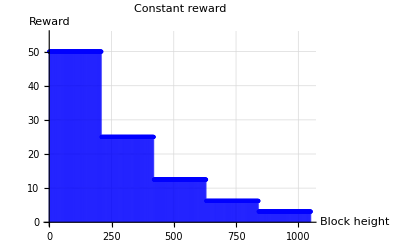

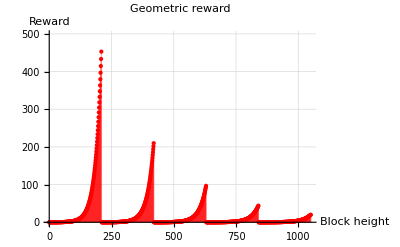

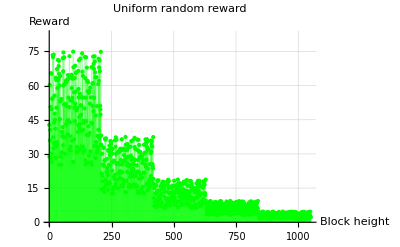

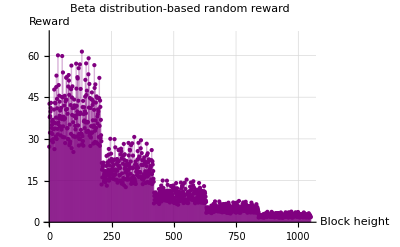

```mathematica
ListPlot[dataconst,PlotRange -> {0, 1.1* Max[dataconst]}, DataRange->{0,sequences*n}, PlotLabel->"Constant reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Blue}]
ListPlot[datageometric,PlotRange -> {0, 1.1* Max[datageometric]}, DataRange->{0,sequences*n}, PlotLabel->"Geometric reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Red}]
ListPlot[datarandom,PlotRange -> {0, 1.1* Max[datarandom]}, DataRange->{0,sequences*n}, PlotLabel->"Uniform random reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Green}]
ListPlot[datarandomdist,PlotRange -> {0, 1.1* Max[datarandomdist]}, DataRange->{0,sequences*n}, PlotLabel->"Beta distribution-based random reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Purple}]
```

## Fairness

Fairness is defined as the proportional reward depending on the starting stake.

## Equitability (Variance)

```mathematica
reward = 50
stake = 1
time = 1000
```

50

1

1000

```mathematica
varianceconst[R_,T_]=Table[R^2/((i+R) (1+R)),{i,1,time}]
variancegeo[R_,T_]=Table[1-((2 (1+R)^(1/i)-1)^i)/(1+R)^2,{i,1,time}]
varianceuniform[R_, T_, rand_] = Table[(rand[[i]]*R)^2/((i+(rand[[i]]*R)) (1+(rand[[i]]*R))),{i,1,time}]
variancebeta[R_, T_, rand_] = Table[(rand[[i]] * R)^2/((i+(rand[[i]]*R)) (1+(rand[[i]]*R))),{i,1,time}]
```

{R^2/(1+R)^2,R^2/((1+R) (2+R)),R^2/((1+R) (3+R)),R^2/((1+R) (4+R)),R^2/((1+R) (5+R)),R^2/((1+R) (6+R)),R^2/((1+R) (7+R)),R^2/((1+R) (8+R)),R^2/((1+R) (9+R)),R^2/((1+R) (10+R)),980,R^2/((1+R) (991+R)),R^2/((1+R) (992+R)),R^2/((1+R) (993+R)),R^2/((1+R) (994+R)),R^2/((1+R) (995+R)),R^2/((1+R) (996+R)),R^2/((1+R) (997+R)),R^2/((1+R) (998+R)),R^2/((1+R) (999+R)),R^2/((1+R) (1000+R))}
 |  |  |  |

{1-(-1+2 (1+R))/(1+R)^2,1-(-1+2 √(1+R))^2/(1+R)^2,996,1-((-1+2 (1+R)^(1/999))^999)/(1+R)^2,1-((-1+2 (1+R)^(1/1000))^1000)/(1+R)^2}
 |  |  |  |

Part::partd: Part specification rand⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{(R^2 rand⟦1⟧^2)/(1+R rand⟦1⟧)^2,(R^2 rand⟦2⟧^2)/((1+R rand⟦2⟧) (2+R rand⟦2⟧)),(R^2 rand⟦3⟧^2)/((1+R rand⟦3⟧) (3+R rand⟦3⟧)),994,(R^2 rand⟦998⟧^2)/((1+R rand⟦998⟧) (998+R rand⟦998⟧)),(R^2 rand⟦999⟧^2)/((1+R rand⟦999⟧) (999+R rand⟦999⟧)),(R^2 rand⟦1000⟧^2)/((1+R rand⟦1000⟧) (1000+R rand⟦1000⟧))}
 |  |  |  |

Part::partd: Part specification rand⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{(R^2 rand⟦1⟧^2)/(1+R rand⟦1⟧)^2,(R^2 rand⟦2⟧^2)/((1+R rand⟦2⟧) (2+R rand⟦2⟧)),(R^2 rand⟦3⟧^2)/((1+R rand⟦3⟧) (3+R rand⟦3⟧)),994,(R^2 rand⟦998⟧^2)/((1+R rand⟦998⟧) (998+R rand⟦998⟧)),(R^2 rand⟦999⟧^2)/((1+R rand⟦999⟧) (999+R rand⟦999⟧)),(R^2 rand⟦1000⟧^2)/((1+R rand⟦1000⟧) (1000+R rand⟦1000⟧))}
 |  |  |  |

```mathematica
datavarconst = varianceconst[reward, time]
datavargeo = variancegeo[reward, time]
datavaruni = varianceuniform[reward,time, RandomVariate[UniformDistribution[{0.5,1.5}], time]]
datavarbeta = variancebeta[reward,time, RandomVariate[BetaDistribution[2,5], time]+0.5]
```

{2500/2601,625/663,2500/2703,1250/1377,500/561,625/714,2500/2907,1250/1479,2500/3009,125/153,2500/3111,1250/1581,2500/3213,625/816,500/663,1250/1683,2500/3417,625/867,2500/3519,250/357,2500/3621,625/918,2500/3723,1250/1887,100/153,625/969,2500/3927,1250/1989,2500/4029,125/204,2500/4131,1250/2091,2500/4233,625/1071,500/867,1250/2193,2500/4437,625/1122,2500/4539,250/459,2500/4641,625/1173,2500/4743,1250/2397,500/969,625/1224,2500/4947,1250/2499,2500/5049,25/51,2500/5151,1250/2601,2500/5253,625/1326,500/1071,1250/2703,2500/5457,625/1377,2500/5559,250/561,2500/5661,625/1428,2500/5763,1250/2907,500/1173,625/1479,2500/5967,1250/3009,2500/6069,125/306,2500/6171,1250/3111,2500/6273,625/1581,20/51,1250/3213,2500/6477,625/1632,2500/6579,250/663,2500/6681,625/1683,2500/6783,1250/3417,500/1377,625/1734,2500/6987,1250/3519,2500/7089,125/357,2500/7191,1250/3621,2500/7293,625/1836,500/1479,1250/3723,2500/7497,625/1887,2500/7599,50/153,2500/7701,625/1938,2500/7803,1250/3927,500/1581,625/1989,2500/8007,1250/4029,2500/8109,125/408,2500/8211,1250/4131,2500/8313,625/2091,500/1683,1250/4233,2500/8517,625/2142,2500/8619,250/867,2500/8721,625/2193,2500/8823,1250/4437,100/357,625/2244,2500/9027,1250/4539,2500/9129,125/459,2500/9231,1250/4641,2500/9333,625/2346,500/1887,1250/4743,2500/9537,625/2397,2500/9639,250/969,2500/9741,625/2448,2500/9843,1250/4947,500/1989,625/2499,2500/10047,1250/5049,2500/10149,25/102,2500/10251,1250/5151,2500/10353,625/2601,500/2091,1250/5253,2500/10557,625/2652,2500/10659,250/1071,2500/10761,625/2703,2500/10863,1250/5457,500/2193,625/2754,2500/11067,1250/5559,2500/11169,125/561,2500/11271,1250/5661,2500/11373,625/2856,100/459,1250/5763,2500/11577,625/2907,2500/11679,250/1173,2500/11781,625/2958,2500/11883,1250/5967,500/2397,625/3009,2500/12087,1250/6069,2500/12189,125/612,2500/12291,1250/6171,2500/12393,625/3111,500/2499,1250/6273,2500/12597,625/3162,2500/12699,10/51,2500/12801,625/3213,2500/12903,1250/6477,500/2601,625/3264,2500/13107,1250/6579,2500/13209,125/663,2500/13311,1250/6681,2500/13413,625/3366,500/2703,1250/6783,2500/13617,625/3417,2500/13719,250/1377,2500/13821,625/3468,2500/13923,1250/6987,100/561,625/3519,2500/14127,1250/7089,2500/14229,125/714,2500/14331,1250/7191,2500/14433,625/3621,500/2907,1250/7293,2500/14637,625/3672,2500/14739,250/1479,2500/14841,625/3723,2500/14943,1250/7497,500/3009,625/3774,2500/15147,1250/7599,2500/15249,25/153,2500/15351,1250/7701,2500/15453,625/3876,500/3111,1250/7803,2500/15657,625/3927,2500/15759,250/1581,2500/15861,625/3978,2500/15963,1250/8007,500/3213,625/4029,2500/16167,1250/8109,2500/16269,125/816,2500/16371,1250/8211,2500/16473,625/4131,100/663,1250/8313,2500/16677,625/4182,2500/16779,250/1683,2500/16881,625/4233,2500/16983,1250/8517,500/3417,625/4284,2500/17187,1250/8619,2500/17289,125/867,2500/17391,1250/8721,2500/17493,625/4386,500/3519,1250/8823,2500/17697,625/4437,2500/17799,50/357,2500/17901,625/4488,2500/18003,1250/9027,500/3621,625/4539,2500/18207,1250/9129,2500/18309,125/918,2500/18411,1250/9231,2500/18513,625/4641,500/3723,1250/9333,2500/18717,625/4692,2500/18819,250/1887,2500/18921,625/4743,2500/19023,1250/9537,20/153,625/4794,2500/19227,1250/9639,2500/19329,125/969,2500/19431,1250/9741,2500/19533,625/4896,500/3927,1250/9843,2500/19737,625/4947,2500/19839,250/1989,2500/19941,625/4998,2500/20043,1250/10047,500/4029,625/5049,2500/20247,1250/10149,2500/20349,25/204,2500/20451,1250/10251,2500/20553,625/5151,500/4131,1250/10353,2500/20757,625/5202,2500/20859,250/2091,2500/20961,625/5253,2500/21063,1250/10557,500/4233,625/5304,2500/21267,1250/10659,2500/21369,125/1071,2500/21471,1250/10761,2500/21573,625/5406,100/867,1250/10863,2500/21777,625/5457,2500/21879,250/2193,2500/21981,625/5508,2500/22083,1250/11067,500/4437,625/5559,2500/22287,1250/11169,2500/22389,125/1122,2500/22491,1250/11271,2500/22593,625/5661,500/4539,1250/11373,2500/22797,625/5712,2500/22899,50/459,2500/23001,625/5763,2500/23103,1250/11577,500/4641,625/5814,2500/23307,1250/11679,2500/23409,125/1173,2500/23511,1250/11781,2500/23613,625/5916,500/4743,1250/11883,2500/23817,625/5967,2500/23919,250/2397,2500/24021,625/6018,2500/24123,1250/12087,100/969,625/6069,2500/24327,1250/12189,2500/24429,125/1224,2500/24531,1250/12291,2500/24633,625/6171,500/4947,1250/12393,2500/24837,625/6222,2500/24939,250/2499,2500/25041,625/6273,2500/25143,1250/12597,500/5049,625/6324,2500/25347,1250/12699,2500/25449,5/51,2500/25551,1250/12801,2500/25653,625/6426,500/5151,1250/12903,2500/25857,625/6477,2500/25959,250/2601,2500/26061,625/6528,2500/26163,1250/13107,500/5253,625/6579,2500/26367,1250/13209,2500/26469,125/1326,2500/26571,1250/13311,2500/26673,625/6681,100/1071,1250/13413,2500/26877,625/6732,2500/26979,250/2703,2500/27081,625/6783,2500/27183,1250/13617,500/5457,625/6834,2500/27387,1250/13719,2500/27489,125/1377,2500/27591,1250/13821,2500/27693,625/6936,500/5559,1250/13923,2500/27897,625/6987,2500/27999,50/561,2500/28101,625/7038,2500/28203,1250/14127,500/5661,625/7089,2500/28407,1250/14229,2500/28509,125/1428,2500/28611,1250/14331,2500/28713,625/7191,500/5763,1250/14433,2500/28917,625/7242,2500/29019,250/2907,2500/29121,625/7293,2500/29223,1250/14637,100/1173,625/7344,2500/29427,1250/14739,2500/29529,125/1479,2500/29631,1250/14841,2500/29733,625/7446,500/5967,1250/14943,2500/29937,625/7497,2500/30039,250/3009,2500/30141,625/7548,2500/30243,1250/15147,500/6069,625/7599,2500/30447,1250/15249,2500/30549,25/306,2500/30651,1250/15351,2500/30753,625/7701,500/6171,1250/15453,2500/30957,625/7752,2500/31059,250/3111,2500/31161,625/7803,2500/31263,1250/15657,500/6273,625/7854,2500/31467,1250/15759,2500/31569,125/1581,2500/31671,1250/15861,2500/31773,625/7956,4/51,1250/15963,2500/31977,625/8007,2500/32079,250/3213,2500/32181,625/8058,2500/32283,1250/16167,500/6477,625/8109,2500/32487,1250/16269,2500/32589,125/1632,2500/32691,1250/16371,2500/32793,625/8211,500/6579,1250/16473,2500/32997,625/8262,2500/33099,50/663,2500/33201,625/8313,2500/33303,1250/16677,500/6681,625/8364,2500/33507,1250/16779,2500/33609,125/1683,2500/33711,1250/16881,2500/33813,625/8466,500/6783,1250/16983,2500/34017,625/8517,2500/34119,250/3417,2500/34221,625/8568,2500/34323,1250/17187,100/1377,625/8619,2500/34527,1250/17289,2500/34629,125/1734,2500/34731,1250/17391,2500/34833,625/8721,500/6987,1250/17493,2500/35037,625/8772,2500/35139,250/3519,2500/35241,625/8823,2500/35343,1250/17697,500/7089,625/8874,2500/35547,1250/17799,2500/35649,25/357,2500/35751,1250/17901,2500/35853,625/8976,500/7191,1250/18003,2500/36057,625/9027,2500/36159,250/3621,2500/36261,625/9078,2500/36363,1250/18207,500/7293,625/9129,2500/36567,1250/18309,2500/36669,125/1836,2500/36771,1250/18411,2500/36873,625/9231,100/1479,1250/18513,2500/37077,625/9282,2500/37179,250/3723,2500/37281,625/9333,2500/37383,1250/18717,500/7497,625/9384,2500/37587,1250/18819,2500/37689,125/1887,2500/37791,1250/18921,2500/37893,625/9486,500/7599,1250/19023,2500/38097,625/9537,2500/38199,10/153,2500/38301,625/9588,2500/38403,1250/19227,500/7701,625/9639,2500/38607,1250/19329,2500/38709,125/1938,2500/38811,1250/19431,2500/38913,625/9741,500/7803,1250/19533,2500/39117,625/9792,2500/39219,250/3927,2500/39321,625/9843,2500/39423,1250/19737,100/1581,625/9894,2500/39627,1250/19839,2500/39729,125/1989,2500/39831,1250/19941,2500/39933,625/9996,500/8007,1250/20043,2500/40137,625/10047,2500/40239,250/4029,2500/40341,625/10098,2500/40443,1250/20247,500/8109,625/10149,2500/40647,1250/20349,2500/40749,25/408,2500/40851,1250/20451,2500/40953,625/10251,500/8211,1250/20553,2500/41157,625/10302,2500/41259,250/4131,2500/41361,625/10353,2500/41463,1250/20757,500/8313,625/10404,2500/41667,1250/20859,2500/41769,125/2091,2500/41871,1250/20961,2500/41973,625/10506,100/1683,1250/21063,2500/42177,625/10557,2500/42279,250/4233,2500/42381,625/10608,2500/42483,1250/21267,500/8517,625/10659,2500/42687,1250/21369,2500/42789,125/2142,2500/42891,1250/21471,2500/42993,625/10761,500/8619,1250/21573,2500/43197,625/10812,2500/43299,50/867,2500/43401,625/10863,2500/43503,1250/21777,500/8721,625/10914,2500/43707,1250/21879,2500/43809,125/2193,2500/43911,1250/21981,2500/44013,625/11016,500/8823,1250/22083,2500/44217,625/11067,2500/44319,250/4437,2500/44421,625/11118,2500/44523,1250/22287,20/357,625/11169,2500/44727,1250/22389,2500/44829,125/2244,2500/44931,1250/22491,2500/45033,625/11271,500/9027,1250/22593,2500/45237,625/11322,2500/45339,250/4539,2500/45441,625/11373,2500/45543,1250/22797,500/9129,625/11424,2500/45747,1250/22899,2500/45849,25/459,2500/45951,1250/23001,2500/46053,625/11526,500/9231,1250/23103,2500/46257,625/11577,2500/46359,250/4641,2500/46461,625/11628,2500/46563,1250/23307,500/9333,625/11679,2500/46767,1250/23409,2500/46869,125/2346,2500/46971,1250/23511,2500/47073,625/11781,100/1887,1250/23613,2500/47277,625/11832,2500/47379,250/4743,2500/47481,625/11883,2500/47583,1250/23817,500/9537,625/11934,2500/47787,1250/23919,2500/47889,125/2397,2500/47991,1250/24021,2500/48093,625/12036,500/9639,1250/24123,2500/48297,625/12087,2500/48399,50/969,2500/48501,625/12138,2500/48603,1250/24327,500/9741,625/12189,2500/48807,1250/24429,2500/48909,125/2448,2500/49011,1250/24531,2500/49113,625/12291,500/9843,1250/24633,2500/49317,625/12342,2500/49419,250/4947,2500/49521,625/12393,2500/49623,1250/24837,100/1989,625/12444,2500/49827,1250/24939,2500/49929,125/2499,2500/50031,1250/25041,2500/50133,625/12546,500/10047,1250/25143,2500/50337,625/12597,2500/50439,250/5049,2500/50541,625/12648,2500/50643,1250/25347,500/10149,625/12699,2500/50847,1250/25449,2500/50949,5/102,2500/51051,1250/25551,2500/51153,625/12801,500/10251,1250/25653,2500/51357,625/12852,2500/51459,250/5151,2500/51561,625/12903,2500/51663,1250/25857,500/10353,625/12954,2500/51867,1250/25959,2500/51969,125/2601,2500/52071,1250/26061,2500/52173,625/13056,100/2091,1250/26163,2500/52377,625/13107,2500/52479,250/5253,2500/52581,625/13158,2500/52683,1250/26367,500/10557,625/13209,2500/52887,1250/26469,2500/52989,125/2652,2500/53091,1250/26571,2500/53193,625/13311,500/10659,1250/26673,2500/53397,625/13362,2500/53499,50/1071}

{2500/2601,1-(-1+2 √51)^2/2601,1-((-1+2 51^(1/3))^3)/2601,995,1-((-1+2 51^(1/999))^999)/2601,1-((-1+2 51^(1/1000))^1000)/2601}
 |  |  |  |

{0.970208,0.958189,0.945039,0.872529,0.91402,0.846913,0.876875,0.746074,0.840709,0.837446,0.833557,0.72705,0.787455,0.669596,0.819786,0.656836,0.615876,0.692691,0.765683,0.687311,0.751064,0.580391,0.662998,0.615197,0.722501,0.676616,0.669171,0.635062,0.460219,0.652099,0.570177,0.614286,0.490423,0.429383,0.416636,0.566168,0.550025,0.434824,0.593842,0.594503,0.631291,0.498602,0.59024,0.571359,0.490409,0.498365,0.454355,0.59056,0.454209,0.537559,0.557588,0.559445,0.475658,0.400875,0.427172,0.526906,0.397208,0.524275,0.519443,0.302995,0.46223,0.375516,0.325612,0.446909,0.427385,0.469632,0.504657,0.277836,0.408528,0.40978,0.389733,0.419935,0.455904,0.482982,0.244211,0.247537,0.468309,0.46963,0.293778,0.290555,0.270533,0.307317,0.240346,0.428197,0.245694,0.441275,0.298127,0.27455,0.340152,0.399273,0.384032,0.265753,0.246628,0.361135,0.40674,0.370956,0.26905,0.200401,0.256526,0.365902,0.395295,0.399692,0.382148,0.227659,0.350064,0.398567,0.254202,0.396441,0.226459,0.301439,0.319534,0.20501,0.309068,0.331576,0.329242,0.27024,0.297979,0.221839,0.293522,0.206552,0.211528,0.310283,0.247454,0.260812,0.165033,0.261055,0.274309,0.318317,0.280702,0.17514,0.288419,0.35057,0.214399,0.21911,0.23724,0.32984,0.231391,0.317189,0.303005,0.284825,0.227212,0.314308,0.229896,0.260519,0.238802,0.296065,0.143599,0.234864,0.275098,0.163633,0.16108,0.313211,0.1389,0.223057,0.246863,0.20315,0.317692,0.302235,0.276517,0.178811,0.245058,0.233739,0.202207,0.168558,0.194075,0.262835,0.238214,0.147581,0.264274,0.289983,0.180285,0.127105,0.263193,0.212097,0.16237,0.140368,0.216188,0.290428,0.240547,0.216231,0.158407,0.149382,0.244909,0.282033,0.275016,0.12656,0.217563,0.281143,0.160724,0.26864,0.117219,0.221489,0.161955,0.122862,0.194496,0.26545,0.153173,0.183158,0.243316,0.211448,0.257053,0.236552,0.249448,0.22839,0.161335,0.157674,0.204225,0.162111,0.196689,0.14819,0.109258,0.152672,0.193453,0.137597,0.242997,0.227509,0.178211,0.138773,0.22686,0.179222,0.138428,0.214593,0.123158,0.242754,0.238459,0.13733,0.169429,0.176726,0.190255,0.207699,0.233195,0.109866,0.137038,0.156157,0.12626,0.186219,0.194032,0.166976,0.130745,0.15382,0.220807,0.186127,0.124672,0.167023,0.221472,0.190865,0.227527,0.164187,0.144244,0.150777,0.186158,0.128604,0.0890849,0.0864421,0.0879623,0.15167,0.15573,0.106655,0.109175,0.168177,0.182722,0.139727,0.216526,0.153388,0.0874376,0.161608,0.172375,0.192938,0.202386,0.0839564,0.207328,0.203415,0.154838,0.093033,0.0825761,0.198008,0.182737,0.0917505,0.16331,0.143733,0.133105,0.165095,0.112377,0.195137,0.124995,0.159534,0.146468,0.189329,0.114431,0.166725,0.167691,0.178933,0.148611,0.0906324,0.107014,0.180784,0.142764,0.188344,0.169357,0.0833727,0.0784232,0.0984581,0.148852,0.0919053,0.0976037,0.152816,0.101584,0.122812,0.174772,0.125399,0.185572,0.0860079,0.18553,0.170554,0.115456,0.0786316,0.104876,0.0998487,0.130186,0.137924,0.182099,0.16541,0.0772152,0.080758,0.0809959,0.175028,0.096487,0.157184,0.0747757,0.0831236,0.105314,0.165245,0.106448,0.130681,0.162824,0.164459,0.132099,0.0668072,0.132325,0.142818,0.0838861,0.140649,0.170406,0.163302,0.123277,0.101271,0.0661192,0.130577,0.173711,0.150523,0.0996528,0.17151,0.138066,0.14345,0.114066,0.117609,0.120093,0.119709,0.152141,0.117289,0.154598,0.091902,0.0840982,0.162093,0.160912,0.0817014,0.0945842,0.151172,0.149859,0.119822,0.0983519,0.132885,0.136727,0.146575,0.0681512,0.0785574,0.159574,0.153853,0.15025,0.160963,0.105295,0.154257,0.13831,0.153712,0.0944013,0.0957424,0.0809612,0.112022,0.125659,0.127406,0.110754,0.0906514,0.102737,0.102711,0.133595,0.0885599,0.0709698,0.107342,0.0829288,0.115853,0.141647,0.147349,0.103592,0.137748,0.0784979,0.0758017,0.140918,0.152066,0.0949862,0.0844435,0.124056,0.104554,0.0792096,0.0698639,0.113301,0.0938392,0.128621,0.0781528,0.0577894,0.0730754,0.0923049,0.145796,0.140043,0.102316,0.0574476,0.0760282,0.139774,0.130895,0.107651,0.120528,0.113072,0.0895171,0.0771478,0.061856,0.133054,0.141565,0.0967133,0.122639,0.109933,0.104423,0.127091,0.140553,0.113664,0.0959465,0.0794711,0.101675,0.0615613,0.137643,0.111921,0.0609853,0.0757626,0.118178,0.0864161,0.127494,0.0667396,0.0648976,0.0854796,0.101351,0.0726451,0.11752,0.0936678,0.116144,0.0543879,0.128235,0.0714152,0.122551,0.0603302,0.108888,0.0746597,0.129804,0.131726,0.0788964,0.11435,0.064625,0.0984598,0.114053,0.0994527,0.102675,0.120653,0.0883413,0.126738,0.103668,0.0497436,0.125601,0.122949,0.0528683,0.0706063,0.109377,0.109995,0.112983,0.101516,0.109291,0.118121,0.12332,0.0704227,0.124784,0.0690703,0.105258,0.058553,0.111334,0.0898716,0.126985,0.0572961,0.118296,0.111301,0.0558495,0.0544968,0.0495061,0.0675049,0.0951438,0.115844,0.0605787,0.0720785,0.045844,0.114978,0.0926071,0.10017,0.0912762,0.0708163,0.0664245,0.0866849,0.101917,0.0525104,0.0906135,0.0896821,0.0723728,0.0988626,0.0916656,0.0781172,0.0629686,0.089076,0.0632867,0.113072,0.0783478,0.0622976,0.0957703,0.0615497,0.108638,0.119177,0.115649,0.0745485,0.0507406,0.0802541,0.0533084,0.0686495,0.0955716,0.0509433,0.050159,0.0947652,0.0919514,0.114892,0.117182,0.109459,0.0676765,0.0966236,0.0633176,0.0849026,0.0928119,0.115894,0.101853,0.0455489,0.109017,0.0614767,0.0546942,0.040938,0.09061,0.0599544,0.065265,0.0940355,0.0997508,0.101953,0.0959316,0.0574465,0.110289,0.0805752,0.0849489,0.0796184,0.104207,0.0451081,0.102413,0.104739,0.0771735,0.0420652,0.0922682,0.0575638,0.110483,0.103678,0.0800879,0.097484,0.105925,0.0540214,0.108724,0.101036,0.0750185,0.0973892,0.108773,0.0761574,0.0689467,0.0881975,0.0884874,0.0592203,0.103295,0.0696781,0.0415201,0.099018,0.0824782,0.0866032,0.092066,0.0879943,0.0785447,0.100127,0.104834,0.0728851,0.0413392,0.0887696,0.0667481,0.104276,0.0655822,0.0589244,0.0518795,0.0949743,0.0400851,0.078048,0.0978781,0.0919527,0.0845111,0.0530926,0.0620944,0.0952552,0.0400474,0.0392839,0.0713837,0.0432246,0.086024,0.0545351,0.0609566,0.0560716,0.0844576,0.10218,0.0705093,0.0568554,0.0522889,0.101857,0.0454278,0.0517246,0.0555853,0.0507203,0.0820541,0.0875489,0.0478392,0.0392916,0.0836314,0.0614671,0.0453178,0.0857987,0.0506432,0.0560201,0.0532786,0.0596569,0.0777545,0.0915915,0.0767042,0.0580678,0.0520195,0.0541123,0.0517773,0.0355104,0.0965759,0.0926792,0.0839669,0.0681599,0.0865112,0.0940158,0.0650233,0.0429554,0.0922909,0.0599279,0.0757391,0.0744589,0.0594286,0.0516406,0.0855661,0.0845501,0.0724189,0.0643125,0.0485696,0.087348,0.0856591,0.0664639,0.086446,0.065503,0.0864557,0.0908111,0.0821948,0.0731007,0.0483212,0.0477196,0.0816064,0.0924492,0.0916458,0.052885,0.075033,0.0612009,0.0494999,0.0621401,0.0421683,0.0513916,0.0845909,0.0824639,0.0896473,0.0650908,0.0429071,0.0575995,0.0358858,0.0632013,0.0712883,0.0364642,0.061297,0.0389634,0.0347956,0.085748,0.0725525,0.089293,0.0490884,0.0410286,0.0543913,0.071058,0.0325053,0.0517228,0.0370998,0.0416104,0.0674987,0.0786216,0.0871555,0.0522827,0.0493445,0.0797399,0.0583182,0.0732365,0.0876978,0.0346216,0.0351425,0.0344384,0.0580806,0.0552777,0.0377728,0.040981,0.0330685,0.0646405,0.0784189,0.0796164,0.0416465,0.0799254,0.0424711,0.0460998,0.038934,0.0388442,0.0643895,0.0494668,0.0857343,0.083707,0.0360531,0.031032,0.0392806,0.0786091,0.0314171,0.0812232,0.0676813,0.0781801,0.0828396,0.0527366,0.0418747,0.0519379,0.0745205,0.0725265,0.0536212,0.078246,0.0390136,0.0681796,0.0818582,0.0339762,0.0745817,0.0841122,0.049727,0.0454926,0.0590953,0.041502,0.0841037,0.0586332,0.065071,0.0732827,0.0723579,0.0848998,0.0578434,0.0576097,0.0458294,0.0328491,0.0332747,0.0841263,0.0608128,0.076891,0.0770452,0.0634044,0.0536225,0.0677808,0.0660873,0.0642484,0.0792506,0.0767788,0.0368715,0.0715736,0.0397365,0.0377868,0.0603754,0.0545078,0.0553419,0.034776,0.0690934,0.0584921,0.0444073,0.0766419,0.0309942,0.0658547,0.0659092,0.0514559,0.0444679,0.0374126,0.0554666,0.0579783,0.0681166,0.061331,0.0644334,0.0631657,0.0412371,0.0726832,0.045217,0.032689,0.0796007,0.0425293,0.0508832,0.0388288,0.0661617,0.0797092,0.0435023,0.067784,0.0456823,0.0716193,0.0751036,0.0303766,0.0777983,0.0297613,0.0554384,0.0422639,0.0614189,0.0787106,0.0545932,0.0616689,0.0559642,0.0335662,0.0390957,0.0491279,0.0445537,0.0520143,0.0455094,0.0468725,0.0632472,0.0505197,0.0324302,0.0334747,0.0563769,0.0441885,0.035593,0.0368967,0.0735596,0.0446247,0.053244,0.0712224,0.0400234,0.0693073,0.0517374,0.0502938,0.049075,0.0590281,0.046493,0.0487281,0.0303608,0.0748782,0.0600422,0.070843,0.0719609,0.0655067,0.069273,0.0676689,0.0697309,0.0354152,0.0523593,0.0410366,0.0641986,0.0570266,0.0588537,0.0428084,0.0435592,0.0367686,0.0541112,0.0279123,0.0736205,0.0709044,0.074693,0.0520604,0.0577838,0.0614647,0.0289646,0.061057,0.0628222,0.0482088,0.038014,0.0528812,0.0552002,0.0527908,0.0658127,0.070555,0.0716153,0.0319726,0.0565257,0.0304543,0.0408839,0.0701648,0.052835,0.0670733,0.0286971,0.0531187,0.058079,0.0584616,0.0441179,0.0322839,0.0275602,0.0299933,0.0462356,0.0252435,0.0288192,0.0347768,0.0282328,0.0319953,0.0669367,0.0535778,0.0662367,0.0428379,0.0453345,0.0592836,0.0283561,0.0292203,0.0396178,0.0689162,0.0641754,0.038998,0.0275278,0.03825,0.038196,0.0567356,0.0364993,0.0367967,0.0262854,0.0504951,0.0315603,0.0507558,0.0402616,0.0470786,0.0317251,0.0474473,0.0683493,0.0359168,0.0441694,0.0264473,0.0402,0.0449508,0.0359353,0.0250786,0.0639767,0.0518755,0.0316819,0.0427473,0.0644081,0.0295754,0.0312382,0.0520409,0.0482262,0.0489086,0.0575575,0.0632194,0.0625677,0.030862,0.0631321,0.0684525,0.0260949,0.0259832,0.0652398,0.0394366,0.0452178,0.0371602,0.0461348}

{0.961198,0.928607,0.912378,0.882486,0.885011,0.812756,0.864116,0.847694,0.775519,0.762969,0.786209,0.760682,0.755883,0.727769,0.662683,0.65627,0.665895,0.749277,0.641666,0.653331,0.595709,0.609262,0.657411,0.610184,0.683491,0.564303,0.532683,0.567306,0.484084,0.507911,0.56893,0.566877,0.552268,0.60706,0.468565,0.464775,0.427848,0.485938,0.445849,0.503423,0.388019,0.547881,0.455787,0.480288,0.426692,0.531368,0.416866,0.469941,0.44499,0.374366,0.394823,0.424071,0.416719,0.41511,0.335093,0.357716,0.32326,0.419087,0.297246,0.391658,0.347425,0.433525,0.326538,0.290725,0.346094,0.383112,0.284057,0.307731,0.307755,0.328917,0.320331,0.365297,0.391767,0.338414,0.345539,0.378499,0.279337,0.37579,0.358655,0.299749,0.271283,0.26414,0.279877,0.265365,0.26844,0.240015,0.264583,0.263178,0.328828,0.347828,0.250243,0.230661,0.369091,0.334357,0.382522,0.266154,0.27044,0.241157,0.288843,0.267421,0.266886,0.276543,0.275806,0.364936,0.248633,0.288382,0.265104,0.33269,0.218084,0.237745,0.20264,0.241178,0.318469,0.222583,0.22951,0.255804,0.23176,0.235491,0.189807,0.247012,0.208635,0.23623,0.27724,0.235167,0.190741,0.309181,0.19928,0.184002,0.200778,0.235862,0.215603,0.28059,0.249528,0.175779,0.240997,0.194178,0.242957,0.242416,0.167311,0.231446,0.194354,0.262954,0.218593,0.165487,0.184452,0.211221,0.184797,0.245656,0.18224,0.186252,0.240939,0.221364,0.197747,0.249323,0.197189,0.243359,0.212868,0.194116,0.249981,0.197368,0.242965,0.201104,0.163706,0.239084,0.160542,0.228641,0.158735,0.253203,0.165641,0.144528,0.169485,0.183316,0.168377,0.198851,0.213554,0.197759,0.194684,0.210045,0.211368,0.148272,0.126386,0.183661,0.16756,0.178497,0.165788,0.203425,0.170876,0.164416,0.263823,0.155543,0.162493,0.132284,0.20803,0.129786,0.120566,0.194526,0.161542,0.123876,0.181362,0.183884,0.165689,0.1184,0.156777,0.14697,0.131974,0.119578,0.131189,0.144147,0.160135,0.164227,0.118244,0.120932,0.119697,0.192983,0.165654,0.150693,0.174419,0.134117,0.154217,0.146023,0.133983,0.217798,0.172091,0.179035,0.113801,0.158548,0.160894,0.132428,0.136163,0.126438,0.106619,0.192791,0.108726,0.111187,0.105929,0.140283,0.151442,0.110645,0.119692,0.116967,0.121013,0.114659,0.113088,0.126565,0.115524,0.12285,0.145332,0.115856,0.116657,0.1205,0.164753,0.164251,0.0991387,0.106559,0.130404,0.100421,0.152496,0.0959724,0.103213,0.113261,0.138133,0.162576,0.169426,0.129056,0.126837,0.169226,0.136179,0.134205,0.117067,0.146414,0.120624,0.0929896,0.152701,0.0878809,0.106363,0.102346,0.163724,0.122774,0.152274,0.0979882,0.116472,0.0923116,0.132046,0.110442,0.0809876,0.117277,0.118238,0.0970953,0.0895997,0.087367,0.112678,0.127261,0.100898,0.129737,0.113406,0.110727,0.0867271,0.0894551,0.11793,0.0917017,0.102029,0.10653,0.10394,0.0790153,0.0887425,0.123933,0.0982902,0.0842015,0.0974203,0.0929169,0.114204,0.124819,0.106402,0.126239,0.0905343,0.156459,0.117252,0.123703,0.128715,0.106024,0.17223,0.0911513,0.146425,0.0903548,0.125181,0.097656,0.119524,0.134348,0.0885428,0.106333,0.0996589,0.125401,0.105745,0.0834917,0.0834371,0.10049,0.127523,0.0916072,0.0993474,0.107465,0.133247,0.101302,0.0997552,0.0959451,0.0927219,0.114146,0.0840025,0.0932615,0.104735,0.107051,0.0956661,0.0952122,0.100292,0.114209,0.0747624,0.126785,0.0889748,0.11388,0.100238,0.0954136,0.0895781,0.0684314,0.0857001,0.105348,0.0814249,0.0716944,0.104634,0.0926006,0.116744,0.082733,0.079421,0.0639659,0.0629694,0.0663162,0.0751069,0.0696129,0.0840484,0.0951544,0.0825204,0.120134,0.0761995,0.0785246,0.0683365,0.0835647,0.0932799,0.112989,0.0791784,0.0958206,0.101974,0.0975304,0.0658522,0.0760324,0.111751,0.0757054,0.107019,0.0871957,0.0771957,0.0935481,0.101503,0.0737237,0.0803529,0.0909378,0.0729349,0.070279,0.105377,0.0752126,0.0768054,0.0825508,0.0887227,0.0988725,0.115973,0.109496,0.0955937,0.0908155,0.126703,0.108301,0.115573,0.0925158,0.0812811,0.0965473,0.0783609,0.0800441,0.0807411,0.0911632,0.0976427,0.0648378,0.0880497,0.0766556,0.0732433,0.0633542,0.0915997,0.0931941,0.0881142,0.0731036,0.0807276,0.0744507,0.0578971,0.0647915,0.0896138,0.0755278,0.120484,0.086986,0.0834446,0.0780688,0.0768994,0.0707948,0.0840132,0.0660997,0.123948,0.0672381,0.0677095,0.0660019,0.0687622,0.0787242,0.065149,0.0648662,0.0561644,0.0514474,0.0815669,0.075283,0.0791285,0.0771695,0.0588049,0.0684831,0.0875325,0.0599254,0.0859363,0.0541286,0.066862,0.0716614,0.105689,0.0513518,0.0969651,0.0740795,0.0837411,0.0849468,0.0847631,0.0902486,0.0632107,0.063921,0.0874983,0.0789151,0.063632,0.0898475,0.064665,0.0681592,0.068048,0.0654963,0.0796448,0.0841509,0.059501,0.0675562,0.0585924,0.0923783,0.0568584,0.0682274,0.0518143,0.0732475,0.0561217,0.0819199,0.0871823,0.0736624,0.0773804,0.0782665,0.0858861,0.0536719,0.0551475,0.0691315,0.0777978,0.053723,0.0523793,0.051094,0.0779391,0.050512,0.0695811,0.0537179,0.0800389,0.056506,0.059399,0.0581433,0.060552,0.0560147,0.0693056,0.0637802,0.0599739,0.0461752,0.0687775,0.0480495,0.0519454,0.049343,0.0648838,0.0679985,0.0749703,0.0556529,0.0638946,0.0645633,0.0575438,0.0585644,0.0726033,0.10986,0.0507392,0.0708269,0.0605694,0.0657133,0.0642789,0.0478952,0.0867485,0.0499656,0.0764768,0.110105,0.0697616,0.073324,0.073815,0.0947924,0.0668552,0.0703763,0.0632718,0.0665829,0.0803994,0.0869738,0.0693598,0.0445653,0.0543378,0.055438,0.0577985,0.0970365,0.0519002,0.0911734,0.0575435,0.074833,0.0640615,0.0689574,0.0459842,0.0524941,0.0840041,0.050643,0.0710687,0.0912243,0.0732544,0.0609975,0.0483077,0.0452151,0.0583254,0.0454501,0.0546275,0.0750425,0.0868033,0.0417554,0.0497591,0.0444683,0.0538188,0.0499012,0.068399,0.0696228,0.0526502,0.0642839,0.0647411,0.0847464,0.0753748,0.0631328,0.0513983,0.0760753,0.0783823,0.0544342,0.0587336,0.0503871,0.0581091,0.0548201,0.0621219,0.0573545,0.0578191,0.0610941,0.0584884,0.0517047,0.0661674,0.0404032,0.0621787,0.0534796,0.0599221,0.0652131,0.0584697,0.0522668,0.0506419,0.0628478,0.0613135,0.0562504,0.0663674,0.0480949,0.0494207,0.0612123,0.055009,0.0651753,0.0417706,0.0825436,0.0573854,0.0713118,0.052594,0.048687,0.0431888,0.0448659,0.0743093,0.0420026,0.0518738,0.0762448,0.0470345,0.0665328,0.0481858,0.0574227,0.0447659,0.0514329,0.0587314,0.0635642,0.0452688,0.0540729,0.0675112,0.0550548,0.0495639,0.0404931,0.0369789,0.0473849,0.0439905,0.0631565,0.0470003,0.0467631,0.0528274,0.0499594,0.0481745,0.071629,0.0599487,0.0515349,0.0467952,0.0445231,0.0615514,0.0530696,0.0461942,0.0500363,0.0582241,0.081592,0.0490237,0.0466098,0.0564266,0.0494882,0.0366447,0.0646547,0.0380577,0.0396726,0.0465161,0.0528039,0.0564125,0.050568,0.0390854,0.0576419,0.0380985,0.0450468,0.0457066,0.0562398,0.0461339,0.0535087,0.0694756,0.0630228,0.0504642,0.0407169,0.0663454,0.045888,0.0646515,0.0418389,0.0430571,0.0505525,0.0373,0.060867,0.0705895,0.0422244,0.0594302,0.0613755,0.0590232,0.0434474,0.0629953,0.0429843,0.055367,0.0575615,0.0590535,0.0508735,0.0587744,0.0532491,0.0633664,0.037222,0.0481595,0.0442292,0.047535,0.0369988,0.0451546,0.0586936,0.070847,0.0509076,0.0352083,0.0533404,0.0592487,0.075137,0.0447679,0.0432098,0.0390027,0.0335465,0.0484944,0.0507233,0.0383536,0.0442994,0.047055,0.0408273,0.0345356,0.045745,0.0442553,0.0487419,0.0622392,0.0766761,0.0468437,0.0476693,0.0418609,0.0418838,0.037859,0.0516491,0.0628568,0.0342228,0.0358114,0.0585968,0.0510248,0.0371118,0.032146,0.0320979,0.0584701,0.0506789,0.044037,0.0341552,0.0526043,0.0347626,0.0397749,0.0398091,0.0599588,0.0339139,0.0500517,0.0493625,0.0374191,0.0460096,0.0597974,0.0356208,0.0361215,0.0677,0.0597326,0.0475833,0.0392831,0.0530405,0.0575185,0.0480945,0.060865,0.0340948,0.0471982,0.0421727,0.0404344,0.0410223,0.0614789,0.048106,0.0318262,0.0549982,0.0598676,0.0398165,0.0452729,0.0569662,0.0396052,0.0592398,0.0456015,0.0471173,0.0344406,0.0456498,0.065463,0.040657,0.0366217,0.0393398,0.0315253,0.0494451,0.0449124,0.0411896,0.0425452,0.0587517,0.0430948,0.050109,0.038789,0.048721,0.0411179,0.0315257,0.0537368,0.0528551,0.0410371,0.0462592,0.0458163,0.0378888,0.0464542,0.0570483,0.0440392,0.0385014,0.0351153,0.0327983,0.0376307,0.0464261,0.0424134,0.0519381,0.0512189,0.0367316,0.040351,0.0380196,0.0423808,0.0438034,0.0340465,0.04013,0.0424703,0.0506194,0.0390565,0.0568884,0.0314266,0.0440284,0.0470969,0.0422507,0.0556826,0.0366051,0.0513407,0.0408198,0.0326077,0.0342657,0.0330693,0.0560677,0.0370937,0.0416721,0.0292394,0.0410041,0.0586016,0.0356942,0.0592625,0.0573704,0.0339825,0.0358148,0.0457391,0.0379094,0.0387392,0.0480753,0.0455787,0.0494386,0.0454185,0.0488006,0.0408413,0.0303961,0.0331953,0.0328126,0.0508978,0.0395705,0.0319897,0.0330925,0.0359545,0.0479259,0.0367964,0.0379294,0.0447098,0.0483383,0.045683,0.0427253,0.03537,0.0322337,0.0284698,0.0350752,0.0384007,0.0528994,0.0570482,0.049359,0.0300408,0.0488298,0.0405783,0.0296321,0.0355178,0.0350898,0.0390188,0.0307564,0.0298808,0.0434239,0.0263249,0.0449338,0.0296142,0.0275461,0.0321228,0.049512,0.0338623,0.0393403,0.0462805,0.0543632,0.045933,0.0559975,0.0313042,0.0432419,0.0411554,0.0388135,0.0531994,0.0356908,0.047307,0.0289636,0.0351176,0.0293122,0.0340478,0.0402111,0.0450151,0.0319601,0.035612,0.0416719,0.0296648,0.0338995,0.0444242,0.0410488,0.0305613,0.0414724,0.0304478,0.0253568,0.0352228,0.0476822,0.035197,0.0352843,0.0451068,0.0327883,0.0291964,0.0294398,0.0346934,0.0325208,0.0389071,0.0404728,0.0458038,0.0335903,0.0297697,0.0282547,0.0524991,0.0408461,0.0272422,0.0462492,0.0289955,0.0305182,0.0304355,0.0322319,0.0358685,0.0487002,0.0253608,0.0544587,0.0523541,0.0464978,0.0381652,0.0340932,0.0260619,0.0481422,0.0367044,0.0293321,0.0321145,0.0323199,0.0353993,0.0300699,0.0279973,0.0490502,0.0340133,0.0345698}

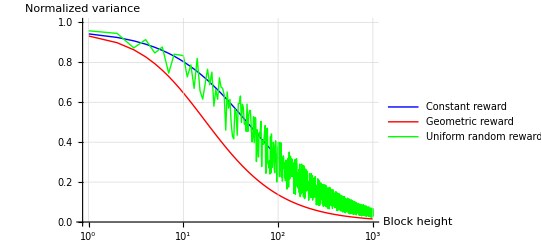

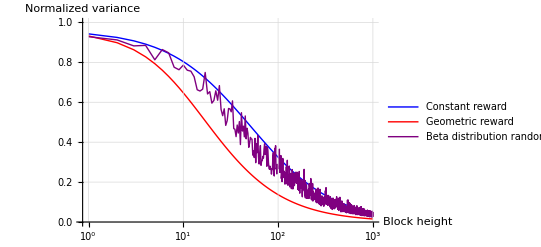

```mathematica
ListLinePlot[{datavarconst, datavargeo, datavaruni},PlotRange -> {0, 1.0}, DataRange->{0,time}, AxesLabel->{"Block height", "Normalized variance"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, PlotStyle-> {Blue, Red, Green}, PlotLegends->{"Constant reward", "Geometric reward", "Uniform random reward"}, ScalingFunctions-> {"Log10", None}]
ListLinePlot[{datavarconst, datavargeo, datavarbeta},PlotRange -> {0, 1.0}, DataRange->{0,time}, AxesLabel->{"Block height", "Normalized variance"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, PlotStyle-> {Blue, Red, Purple}, PlotLegends->{"Constant reward", "Geometric reward", "Beta distribution random reward"}, ScalingFunctions-> {"Log10", None}]
```